# Birefringent Object Generator for Light Field Imaging by Rudolf Oldenbourg , Marine Biological Laboratory, Woods Hole, Massachusetts Dec 2022, May 2023, June 2023

### Introductory Note

This Notebook defines functions that generate arrays of objects intended for simulating their polarized light field images.
To see the Notes, graphics, code, etc., you need to expand the cells grouped under their headings Objects, Composites, Export objects as HDF5 file, Graphics for light field camera,etc.. The latter is some bonus code for generating graphical representations of light field imaging instrumentation and concepts.
To view the Mathematica Notebook, read explanatory text, view images, and interact with existing graphics objects, readers can use the Wolfram Player https://www.wolfram.com/player, a software application that can be freely downloaded from the Wolfram website.
To work with the code and generate your own sample objects, you need Mathematica and some understanding of its syntax.

#### A note on array dimensions and axis orientations

In all my Notebooks about ray tracing simulations for microscopy, the microscope optical axis is oriented parallel to the X-axis. The elements (voxels) of a 3D object array are addressed by indices i1, i2, and i3: object[[i1,i2,i3]]. Index i1 enumerates the voxels along the Z-axis, i2 along the Y-axis, and i3 along the X-axis. For example, the array that holds the birefringence values (typically smp[[2]]) has a a single birefringence value for each voxel identified by i1, i2, and i3. The array that holds the optic axis direction (typically smp[[3]]) has a triplet of numbers for each voxel identified by i1 (along Z), i2 (along Y), and i3 (along X). The triplet of numbers are the (X,Y,Z} components of a unit vector. Note that the vector components are given in the reverse order compared to the object array indices.

```mathematica
?bundleBir
```

```mathematica
smp=bundleBir[2.5,7,-0.01,90°,0°];
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Module[{x,y,z},x=0; y=0; z=0;  (*{x,y,z} displacement vector of the lower left corner*)bundleXΔn={FaceForm[],Cuboid[{x,y,z},{x,y,z}+smp[[1,2]]],Raster3D[smp[[2]]/smp[[1,8]],{{x,y,z},{x,y,z}+smp[[1,2]]},ColorFunction->"GrayLevelOpacity"]};
bundleXOpticAxis=Translate[{FaceForm[],Cuboid[{0,0,0},smp[[1,2]]],Red,Map[Line,tmp]},{x+9,y,z}]];

smp=bundleBir[2.5,7,-0.01,0°,0°];
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Module[{x,y,z},x=20; y=0; z=0;  (*{x,y,z} displacement vector of the lower left corner*)bundleYΔn={FaceForm[],Cuboid[{x,y,z},{x,y,z}+smp[[1,2]]],Raster3D[smp[[2]]/smp[[1,8]],{{x,y,z},{x,y,z}+smp[[1,2]]},ColorFunction->"GrayLevelOpacity"]};
bundleYOpticAxis=Translate[{FaceForm[],Cuboid[{0,0,0},smp[[1,2]]],Red,Map[Line,tmp]},{x+7,y,z}]];

smp=bundleBir[2.5,7,-0.01,0°,90°];
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Module[{x,y,z},x=36; y=0; z=0;  (*{x,y,z} displacement vector of the lower left corner*)bundleZΔn={FaceForm[],Cuboid[{x,y,z},{x,y,z}+smp[[1,2]]],Raster3D[smp[[2]]/smp[[1,8]],{{x,y,z},{x,y,z}+smp[[1,2]]},ColorFunction->"GrayLevelOpacity"]};
bundleZOpticAxis=Translate[{FaceForm[],Cuboid[{0,0,0},smp[[1,2]]],Red,Map[Line,tmp]},{x+7,y,z}]];

smp=bundleBir[2.5,7,-0.01,45°,45°];
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Module[{x,y,z},x=52; y=0; z=0;  (*{x,y,z} displacement vector of the lower left corner*)bundleXYZΔn={FaceForm[],Cuboid[{x,y,z},{x,y,z}+smp[[1,2]]],Raster3D[smp[[2]]/smp[[1,8]],{{x,y,z},{x,y,z}+smp[[1,2]]},ColorFunction->"GrayLevelOpacity"]};
bundleXYZOpticAxis=Translate[{FaceForm[],Cuboid[{0,0,0},smp[[1,2]]],Red,Map[Line,tmp]},{x+10,y,z}]];

Graphics3D[{
Text[Style["bundleX\n",Bold,18],{10,7,7}],bundleXΔn,bundleXOpticAxis,
Text[Style["bundleY\n",Bold,18],{7+20,7,8}],bundleYΔn,bundleYOpticAxis,
Text[Style["bundleZ\n",Bold,18],{7+36,7,8}],bundleZΔn,bundleZOpticAxis,
Text[Style["bundleXYZ\n",Bold,18],{7+57,7,13}],bundleXYZΔn,bundleXYZOpticAxis,
Thick,Arrowheads[0.02],Arrow[{{-2,-2,-2},{7,-2,-2}}],Text["X",{3.5,-4,-2}],Arrow[{{-2,-2,-2},{-2,7,-2}}],Text["Y",{-3,2,-2}],Arrow[{{-2,-2,-2},{-2,-2,7}}],Text["Z",{-3.5,-2,2}]},Boxed->False]
```

-Graphics3D-

### Objects All lengths given in units of the voxel size, also called voxPitch, with voxPitch the same in X-, Y-, and Z-direction All angles in radian

All sample functions and their composites generate a list that has three elements on the first level: The first element is a list of metadata such as the object size in voxPitch units, and the voxPitch in µm that was used to generate the sample list. To show the metadata, print the first list element. The second element is a 3D list of the birefringence (a scalar) of each voxel of the sample. The third element is a 3D list of a 3D vector for each voxel, where each vector indicates the orientation of the optic axis of a birefringent voxel. When the birefringence is zero, the vector is {0,0,0}. The second and third elements are 3D lists with the same number of elements, namely the number of voxels that represent the sample object.
In the list of metadata, the second element must be the list of X, Y, and Z numbers of voxels in the x-, y-, and z-directions. {X, Y, Z} represents the size of the box that contains the object.

#### Birefringent ball, ballBir[radius,Δn,theta,azim], is a solid ball made of birefringent (Δn≠0) material. The ball’s diameter is made to be an odd number of voxPitch, including one, with its center in the center of a voxel (radius=0 will result in a ball radius of 0.5 voxPitch). The material has an optic axis, whose orientation is defined by angles azim and theta and is represented by a vector of length 1. For azim=theta=0, the optic axis is oriented parallel to the x-axis. The axis can be rotated around the y-axis by the angle theta [in radian] away from the x-axis, and then rotated by azim [in radian] around the x-axis. The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. Δn and the optic axis are the same for every voxel of the ball. The birefringence of voxels near the edge of the object can be fractions of Δn.

```mathematica
ballBir::usage="ballBir[radius,Δn,theta,azim], is a solid ball made of birefringent (Δn≠0) material. Angles in radian and radius in units of voxPitch.
The ball's diameter is made to be an odd number of voxPitch, including one, with its center in the center of a voxel (radius=0 will result in a ball radius of 0.5 voxPitch). 
The material has an optic axis, whose orientation is defined by angles azim and theta (in radian) and is represented by a vector of length 1. 
For azim=theta=0, the optic axis is oriented parallel to the x-axis. The axis can be rotated around the y-axis by the angle theta away from the x-axis, and then rotated by azim [in radian] around the x-axis. 
The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. Δn and the optic axis are the same for every voxel of the ball. The birefringence of voxels near the edge of the object can be fractions of Δn.";

ballBir[radius_,Δn_,theta_,azim_]:=
Module[{r,rotAzim,rotTheta,smpRegion,smpBounds,rSize,ΔnArray,opticAxis,opticAxisArray},
If[radius==0,r=0.5,r=radius];
rotTheta=RotationMatrix[theta,{0,1,0}];
rotAzim=RotationMatrix[azim ,{1,0,0}];
opticAxis=rotAzim.(rotTheta.{1,0,0});
smpRegion=Region@Ball[{0,0,0},r];
smpBounds=RegionBounds[smpRegion];
rSize=Ceiling[(Transpose[smpBounds][[2]]-Transpose[smpBounds][[1]])];Do[If[EvenQ[rSize[[i]]],rSize[[i]]+=1],{i,3}];(*raster size, it changes the radius to an integer number of voxels plus 0.5*)
ΔnArray=Reverse[ImageData[RegionImage[smpRegion,RegionBounds[smpRegion],RasterSize->rSize]]Δn,{1,2}];
opticAxisArray=Table[If[ΔnArray[[k,j,i]]≠0,opticAxis,{0,0,0}],{k,rSize[[3]]},{j,rSize[[2]]},{i,rSize[[1]]}]; (*array of normalized vectors*)
{{"Ball box {X,Y,Z}=",rSize,", radius=",rSize[[1]]/2//N,", all in units of voxPitch, birefringence=",Δn,", rotation theta=",theta,", rotation azim=",azim},ΔnArray,opticAxisArray}]
```

Graphics

```mathematica
?ballBir
```

```mathematica
smp=ballBir[0,-0.01,0°,0°];
Print@@smp[[1]];
Graphics3D[Raster3D[smp[[2]]/(2If[smp[[1,6]]<0,Min[smp[[2]]],Max[smp[[2]]]]),ColorFunction->"GrayLevelOpacity"]]
tmp2=DeleteCases[Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2],Null];
Graphics3D[{Red,Map[Line,tmp2]},ImageSize->200]
```

Ball box {X,Y,Z}={1,1,1}, radius=0.5, all in units of voxPitch, birefringence=-0.01, rotation theta=0, rotation azim=0

-Graphics3D-

-Graphics3D-

#### Birefringent sheet, sheetBir[radius,thickness,Δn,theta,azim], angles in radian, radius and thickness in units of voxPitch of a birefringent (Δn) sheet (cylinder) that extends in the y-z plane. Its optic axis opticAxis has an inclination angle theta to x-axis and an azimuth angle (azim) in the y-z plane measured from the z-axis. The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. Δn and the optic axis are the same for every voxel of the sheet. The birefringence of voxels near the edge of the object can be fractions of Δn. Stack of birefringent sheets, stackBir[{sheetBir[],sheetBir[],...}]

```mathematica
sheetBir::usage="sheetBir[radius,thickness,Δn,theta,azim], angles in radian, radius and thickness in units of voxPitch of a birefringent (Δn) sheet (cylinder) that extends in the y-z plane. 
A radius ending in .5 puts the center of the sheet in the center of a voxel in the Y-Z plane
An odd integer thickness puts the center of the sheet in the center of a voxel in the X-direction";

sheetBirStack::usage="sheetBirStack[sheetList] combines a stack of birefringent sheets into a single object. The input is a list of sheetBir[]functions 
each of which has as input the thickness, Δn, and optic axis orientation of the individual sheet. All sheets must have the same radius.
sheetBirStack[] combines the ΔnArrays and opticAxisArrays of the individual sheets and converts them to a single object";

sheetBir[radius_,thick_,Δn_,theta_,azim_]:=
Module[{opticAxis,rotAzim,rotTheta,smpRegion,smpBounds,rSize,ΔnArray,opticAxisArray},
rotTheta=RotationMatrix[theta,{0,1,0}];
rotAzim=RotationMatrix[azim,{1,0,0}];
opticAxis=Normalize[rotAzim.(rotTheta.{1,0,0})];
smpRegion=Region@Cylinder[{{-thick/2,0,0},{thick/2,0,0}},radius];
smpBounds=RegionBounds[smpRegion];
rSize=Round[(Transpose[smpBounds][[2]]-Transpose[smpBounds][[1]])];
ΔnArray=Reverse[ImageData[RegionImage[smpRegion,RegionBounds[smpRegion],RasterSize->rSize]]Δn,{1,2}];
opticAxisArray=Table[If[ΔnArray[[k,j,i]]≠0,opticAxis,{0,0,0}],{k,rSize[[3]]},{j,rSize[[2]]},{i,rSize[[1]]}];
{{"Sheet box {X,Y,Z}=",rSize,", radius=",radius,", sheet thickness=",thick,", all in units of voxPitch, birefringence=",Δn,", rotation theta=",theta,", rotation azim=",azim} ,ΔnArray,opticAxisArray}]

sheetBirStack[sheetList_]:=
Catch[Module[{num,thickList,r,ΔnList,stackThick,smpRegion,smpBounds,rSize,ΔnArray,opticAxisArray},
num=Length[sheetList];(*number of sheets in the stack*)
r=sheetList[[1,1,4]]; If[Table[r,num]≠Table[sheetList[[i,1,4]],{i,num}],Throw["All sheets must have the same radius"]];
ΔnList=Table[sheetList[[i,1,8]],{i,num}];
thickList=Table[sheetList[[i,1,6]],{i,num}];
stackThick=Plus@@thickList;
ΔnArray=Transpose[sheetList[[1,2]],{3,2,1}];
opticAxisArray=Transpose[sheetList[[1,3]],{3,2,1}];
For[i=2,i≤num,i++,
	ΔnArray=Join[ΔnArray,Transpose[sheetList[[i,2]],{3,2,1}]];
	opticAxisArray=Join[opticAxisArray,Transpose[sheetList[[i,3]],{3,2,1}]]
	];
ΔnArray=Transpose[ΔnArray,{3,2,1}];
opticAxisArray=Transpose[opticAxisArray,{3,2,1}];
rSize=Reverse[Dimensions[ΔnArray]];
{{"Sheet stack box {X,Y,Z}=",rSize,", radius=",r,", number of sheets = ",num,", Δn List =",ΔnList,", stack thickness = ",stackThick,", all length in units of voxPitch"},ΔnArray,opticAxisArray}]]
```

Graphics

```mathematica
?sheetBir
```

```mathematica
?sheetBirStack
```

```mathematica
sheetRadius=7.5;
sheetBirList1={sheetBir[3.5,3,0.1,0°,0°]};
sheetBirList2={sheetBir[sheetRadius,2,0.2,0°,0°],sheetBir[sheetRadius,4,0.1,90°,0°]};
sheetBirList3={sheetBir[7.5,3,0.1,0°,0°],sheetBir[7.5,1,0.2,90°,0°],sheetBir[7.5,2,0.05,45°,45°]};
```

```mathematica
smp[[1]]
```

{Sheet stack box {X,Y,Z}=,{6,15,15},, radius=,7.5,, number of sheets = ,3,, Δn List =,{0,90 °,45 °},, stack thickness = ,6,, all length in units of voxPitch}

```mathematica
(*smp=sheetBir[sheetRadius,3,0.1,10°,0];*)
smp=sheetBirStack[sheetBirList3];
Catch[If[%=="All sheets must have the same radius",Throw["All sheets must have the same radius"]];
Print@@smp[[1]];
If[smp[[1,1]]=="Sheet box {X,Y,Z}=",Graphics3D[Raster3D[smp[[2]]/smp[[1,8]],ColorFunction->"GrayLevelOpacity"]]//Print];
If[smp[[1,1]]=="Sheet stack box {X,Y,Z}=",ΔnMax=Max[smp[[1,8]]];Graphics3D[Raster3D[smp[[2]]/ΔnMax,ColorFunction->"GrayLevelOpacity"]]//Print];
tmp1=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{Red,Map[Line,tmp1]},ImageSize->200]]
```

Sheet stack box {X,Y,Z}={6,15,15}, radius=7.5, number of sheets = 3, Δn List ={0.1,0.2,0.05}, stack thickness = 6, all length in units of voxPitch

-Graphics3D-

-Graphics3D-

#### Birefringent cuboid, cuboidBir[sideX,sideY,sideZ,Δn,theta,azim], with sides of length sideX, sideY, sideZ in units of voxPitch, and birefringence Δn. Its optic axis opticAxis has a tilt angle theta to the x-axis and an azimuth angle (azim) in the y-z plane measured from the z-axis. The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. Δn and the optic axis are the same for every voxel of the cuboid. Series of birefringent cuboids stacked along the Y direction stackYCuboidBir[cuboidList]

```mathematica
cuboidBir::usage="cuboidBir[sideX,sideY,sideZ,Δn,theta,azim], angles in radian, length in units of voxPitch, and birefringence Δn. 
A birefringent cuboid whose optic axis opticAxis has a tilt angle theta to the x-axis and an azimuth angle (azim) in the y-z plane measured from the z-axis. 
The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. Δn and the optic axis are the same for every voxel of the cuboid.";

cuboidStackYBir::usage="cuboidStackYBir[cuboidList] combines a list of cuboids into a single object that represents a stack along Y of birefringent cuboids separated along Y; 
all cuboids must have the same dimensions in X and Z, but can differ in Y and in their Δn values and slow axis orientations";

cuboidBir[sideX_,sideY_,sideZ_,Δn_,theta_,azim_]:=
Module[{opticAxis,rotAzim,rotTheta,smpRegion,smpBounds,cuboidBox,ΔnArray,opticAxisArray},
rotTheta=RotationMatrix[theta,{0,1,0}];
rotAzim=RotationMatrix[azim,{1,0,0}];
opticAxis=Normalize[rotAzim.(rotTheta.{1,0,0})];
cuboidBox={sideX,sideY,sideZ}//Round;
ΔnArray=Table[Δn,{k,cuboidBox[[3]]},{j,cuboidBox[[2]]},{i,cuboidBox[[1]]}];
opticAxisArray=Table[If[ΔnArray[[k,j,i]]≠0,opticAxis,{0,0,0}],{k,cuboidBox[[3]]},{j,cuboidBox[[2]]},{i,cuboidBox[[1]]}];
{{"cuboid box {X,Y,Z}=",cuboidBox,", in units of voxPitch, birefringence=",Δn,", rotation theta=",theta,", rotation azim=",azim},ΔnArray,opticAxisArray}]

cuboidStackYBir[cuboidList_]:=
Catch[Module[{num,sideYList,sideYStack,ΔnList,stackThick,smpRegion,smpBounds,stackBox,ΔnArray,opticAxisArray},
num=Length[cuboidList];(*number of cuboids in the stack*)
 If[Table[{cuboidList[[1,1,2,1]],cuboidList[[1,1,2,3]]},num]≠Table[{cuboidList[[i,1,2,1]],cuboidList[[i,1,2,3]]},{i,num}],Throw["All cuboids must have the same X and Z dimension"]];
ΔnList=Table[cuboidList[[i,1,6]],{i,num}];
sideYList=Table[cuboidList[[i,1,2,2]],{i,num}];
sideYStack=Plus@@sideYList;
ΔnArray=Transpose[cuboidList[[1,2]],{2,1,3}];
opticAxisArray=Transpose[cuboidList[[1,3]],{2,1,3}];
For[i=2,i≤num,i++,
	ΔnArray=Join[ΔnArray,Transpose[cuboidList[[i,2]],{2,1,3}]];
	opticAxisArray=Join[opticAxisArray,Transpose[cuboidList[[i,3]],{2,1,3}]]
	];
ΔnArray=Transpose[ΔnArray,{2,1,3}];
opticAxisArray=Transpose[opticAxisArray,{2,1,3}];
stackBox=Reverse[Dimensions[ΔnArray]];
{{"stackYCuboid box {X,Y,Z}=",stackBox,", in units of voxPitch, number of cuboids = ",num,", Δn List =",ΔnList},ΔnArray,opticAxisArray}]]
```

Graphics

```mathematica
?cuboidBir
```

```mathematica
smp=cuboidBir[3,3,9,0.1,0,0];
```

```mathematica
cuboidList1={cuboidBir[3,3,9,0.1,0,0]};
cuboidList3={cuboidBir[1,9,9,0.1,0,0],cuboidBir[1,6,9,0.0,0,0],cuboidBir[1,3,9,0.08,90,0]};
cuboidList5={cuboidBir[3,3,9,0.1,0,0],cuboidBir[3,6,9,0.0,90,0],cuboidBir[3,3,9,0.08,90,0],
			cuboidBir[3,6,9,0.0,90,0],cuboidBir[3,3,9,0.04,90,45]};
```

```mathematica
smp=cuboidStackYBir[cuboidList3];
```

```mathematica
?cuboidStackYBir
```

```mathematica
smp=cuboidStackYBir[cuboidList3];
Catch[If[%=="All cuboids must have the same X and Z dimension",Throw["All cuboids must have the same X and Z dimension"]];
Print@@smp[[1]];
If[smp[[1,1]]=="cuboid box {X,Y,Z}=",Graphics3D[Raster3D[smp[[2]]/(1.2smp[[1,6]]),ColorFunction->"GrayLevelOpacity"]]//Print];
If[smp[[1,1]]=="stackYCuboid box {X,Y,Z}=",ΔnMax=Max[smp[[1,8]]];Graphics3D[Raster3D[smp[[2]]/(1.2ΔnMax),ColorFunction->"GrayLevelOpacity"]]//Print];
tmp1=DeleteCases[Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2],Null];
Graphics3D[{Red,Map[Line,tmp1]},ImageSize->200]]
```

stackYCuboid box {X,Y,Z}={1,18,9}, in units of voxPitch = 1µm, number of cuboids = 3, Δn List ={0.1,0.,0.08}

-Graphics3D-

-Graphics3D-

#### Birefringent GUV (Giant Unilamellar Vesicle), guvBir[guvRadius,membraneThickness,Δn] is a Giant Unilamellar Vesicle. The membrane is birefringent (due to the lipid molecules and/or embedded proteins, for example) with an optic axis, whose orientation is normal to the local membrane. The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. Δn is the same for every fully occupied voxel of the membrane. The birefringence of voxels near the edge of the object can be fractions of Δn.

```mathematica
guvBir::usage="guvBir[guvRadius,membraneThickness,Δn] is a Giant Unilamellar Vesicle whose membrane is birefringent (due to the lipid molecules and/or embedded proteins, for example) 
with an optic axis, whose orientation is normal to the local membrane. 
The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. 
Δn is the same for every fully occupied voxel of the membrane. The birefringence of voxels near the edge of the object can be fractions of Δn.";

guvBir[guvRadius_,membraneThickness_,Δn_]:=
Module[{gC,gR,mT,i1,i2,ΔnArray,guvBox,voxNr,tmp,opticAxisArray},
gR=Floor[guvRadius]+0.5;  (*ensures that gR reaches the edge of a voxel in x,y,z directions*)
mT=Floor[membraneThickness];
guvBox=If[OddQ[tmp=Ceiling[2gR]],(tmp+2){1,1,1},(tmp+1){1,1,1}];
gC=guvBox/2;
i1=RegionImage[Ball[gC,gR],Transpose[{{0,0,0},guvBox}],RasterSize->guvBox];
i2=RegionImage[Ball[gC,gR-mT],Transpose[{{0,0,0},guvBox}],RasterSize->guvBox];
ΔnArray=Reverse[ImageData[ImageSubtract[i1,i2]//ImageClip]Δn,{1,2}];
opticAxisArray=Table[If[ΔnArray[[k,j,i]]==0,{0,0,0},Normalize[{i-0.5,j-0.5,k-0.5}-gC]],{k,guvBox[[3]]},{j,guvBox[[2]]},{i,guvBox[[1]]}];
{{"GUV box {X,Y,Z}=",guvBox,", GUV radius=",gR,", membrane thick=",mT,", all in units of voxPitch, Δn=",Δn},ΔnArray,opticAxisArray}]
```

Graphics

```mathematica
?guvBir
```

```mathematica
smp=guvBir[3,1,0.1];
Print@@smp[[1]];
Graphics3D[Raster3D[smp[[2]]/smp[[1,-1]],ColorFunction->"GrayLevelOpacity"]]
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{Red,Map[Line,tmp]},ImageSize->200]
```

GUV box {X,Y,Z}={9,9,9}, GUV radius=3.5, membrane thick=1, all in units of voxPitch, Δn=0.1

-Graphics3D-

-Graphics3D-

#### Birefringent shell, shellBir[outerRadius,innerRadius,ctrDispl,shellHeight,Δn] is simulating a juvenile clam shell. The code is derived from guvBir[...] by cutting off the bottom part of the sphere, leaving the top cap of height shellHeight. The shell is birefringent with an optic axis, whose orientation is normal to the local outer shell surface. The birefringence Δn can be positive or negative, and if Δn=0, the optic axis is {0,0,0}. Δn is the same for every fully occupied voxel of the shell. The birefringence of voxels near the edge of the object can be fractions of Δn.

```mathematica
shellBir::usage="shellBir[outerRadius,innerRadius,ctrDispl,shellHeight,Δn] is a birefringent shell defined by an outer surface with radius outerRadius,
an inner surface with radius innerRadius, whose centers can be displaced by ctrDispl, eg. {0,0,0}, and the shell height, all in units of voxPitch
shellBir roughly corresponds to the top cap of a GUV, with height specifying the height of the cap (height < 2*shellRadius)
If the centers of the two spherical surfaces is the same (ctrDispl={0,0,0}), then the thickness of the shell is uniform and equal to outerRadius-innerRadius";

shellBir[outerRadius_,innerRadius_,ctrDispl_,shellHeight_,Δn_]:=
Module[{oR,iR,shH,shC,i1,i2,i12,i3,i123,shellBox,tmp,ΔnArray,opticAxisArray},
oR=Ceiling[outerRadius]+0.5;  (*ensures that the outer radius reaches the edge of a voxel in x,y,z directions*)
iR=Floor[innerRadius]+0.5;  (*ensures that the outer radius reaches the edge of a voxel in x,y,z directions*)
shH=Ceiling[shellHeight+1];  (*ensures that shellHeight is an interger number of voxels*)
shellBox=If[OddQ[tmp=Ceiling[2oR]],(tmp+2){1,1,1},(tmp+1){1,1,1}];
shC=shellBox/2;
i1=RegionImage[Ball[shC,oR],Transpose[{{0,0,0},shellBox}],RasterSize->shellBox];
i2=RegionImage[Ball[shC+Round[ctrDispl],iR],Transpose[{{0,0,0},shellBox}],RasterSize->shellBox];
i12=ImageSubtract[i1,i2];
(*Cut the portion 2*oR-shellHeight away*)
i3=RegionImage[Cylinder[{shC-{oR+2,0,0},shC+(oR-shH){1,0,0}},oR+1],Transpose[{{0,0,0},shellBox}],RasterSize->shellBox];
i123=ImageSubtract[i12,i3]//ImageClip;
ΔnArray=Reverse[ImageData[i123]×Δn,{1,2}];
ΔnArray=Drop[ΔnArray,0,0,tmp=2oR-shH;If[OddQ[tmp],tmp-1,tmp]];
shellBox=Reverse[Dimensions[ΔnArray]];
shC=shC+{-(shC[[1]]+(oR-shH)),0,0};
opticAxisArray=Table[If[ΔnArray[[k,j,i]]==0,{0,0,0},Normalize[{i-0.5,j-0.5,k-0.5}-shC]],{k,shellBox[[3]]},{j,shellBox[[2]]},{i,shellBox[[1]]}];
{{"Shell box {X,Y,Z}=",shellBox,", shell outer radius=",oR,", shell inner radius=",iR,", radius center displacement=",ctrDispl,", shell height=",shH-1,", all in units of voxPitch, Δn=",Δn},ΔnArray,opticAxisArray}]
```

Graphics

```mathematica
?shellBir
```

```mathematica
(*voxPitch=µLensPitch, 40voxPitch=69µm, 32voxPitch=55µm, 11voxPitch=19µm*)
smp=shellBir[20,18,{0,0,0},5,-0.1];
```

```mathematica
(*voxPitch=µLensPitch/3, 35voxPitch=20µm, used in simulation for JOSAA article in 2022*)
smp=shellBir[120,117,{2,0,0},35,-0.172];
```

Shell box {X,Y,Z}={8,43,43}, shell outer radius=20.5, shell inner radius=18.5, radius center displacement={0,0,0}, shell height=5, all in units of voxPitch, Δn=-0.1

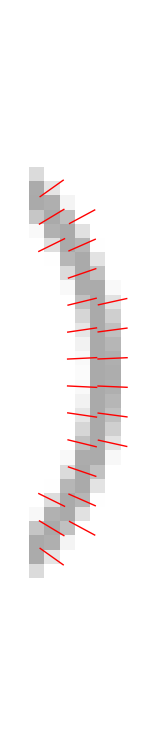

```mathematica
Print@@smp[[1]];
yPosXZSlice=Round[smp[[1,2,2]]/2];  (*Y position of X-Z slice*)
scaleLine=2;  (*1 draws a line every voxel, 2 every second voxel, etc.*)
lineList=DeleteCases[Flatten[Table[If[smp[[2,j,yPosXZSlice,i]]≠0,deltaLine=scaleLine Drop[smp[[3,j,yPosXZSlice,i]],{2}]/2;{{i-0.5,j-0.5}-deltaLine,{i-0.5,j-0.5}+deltaLine}],
			{i,1,smp[[1,2,1]],scaleLine},{j,1,smp[[1,2,3]],scaleLine}],1],Null];
Graphics[{Raster[Abs[smp[[2,All,yPosXZSlice,All]]/smp[[1,-1]]/3-1]],Red,Map[Line,lineList]}]
```

```mathematica
Print@@smp[[1]];
Graphics3D[Raster3D[Abs[smp[[2]]/smp[[1,-1]]],ColorFunction->"GrayLevelOpacity"],Boxed->False]
(*tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{Red,Map[Line,tmp]},ImageSize->200]*)
```

Shell box {X,Y,Z}={8,43,43}, shell outer radius=20.5, shell inner radius=18.5, radius center displacement={0,0,0}, shell height=5, all in units of voxPitch, Δn=-0.1

-Graphics3D-

#### Birefringent bundle, bundleBir[radius,length,Δn,theta,azim], radius and length of a straight bundle (cylinder), inclination angle theta and azimuth azim of the bundle axis. For theta = azim = 0, the bundle axis is parallel the y-axis. The bundle material is birefringent with an optic axis that is parallel to the bundle axis. The birefringence Δn can be positive or negative, and if Δn=0 the optic axis is {0,0,0}. Δn is the same for every fully occupied voxel of the membrane. The birefringence of voxels near the edge of the object can be fractions of Δn.

```mathematica
bundleBir::usage="bundleBir[radius,length,Δn,theta,azim], radius and length of a straight bundle (cylinder). For theta = azim = 0, the bundle axis is parallel the y-axis. The center of the bundle is in the center of a voxel. 
The bundle axis is inclined by theta away from the y-z plane and rotated by azim around the x-axis, both in radian.  
The bundle material is birefringent with an optic axis that is parallel to the bundle axis. The birefringence Δn can be positive or negative, and if Δn=0 the optic axis is {0,0,0}. 
Δn is the same for every fully occupied voxel of the membrane. The birefringence of voxels near the edge of the object can be fractions of Δn.";

bundleBir[radius_,length_,Δn_,theta_,azim_]:=
Module[{r,l,bAxis,rotTheta,rotAzim,smpRegion,smpBounds,rSize, ΔnArray,opticAxisArray},
r=(Floor[radius]+0.5);
l=If[EvenQ[length],length+1,length];  (*the r and l values make sure that the bundle center is in the center of a voxel*)
rotTheta=RotationMatrix[theta,{0,0,1}];
rotAzim=RotationMatrix[azim,{1,0,0}];
bAxis={rotAzim.(rotTheta.{0,-l/2,0}),rotAzim.(rotTheta.{0,l/2,0})};
smpRegion=Region@Cylinder[bAxis,r];
smpBounds=RegionBounds[smpRegion];
rSize=Ceiling[(Transpose[smpBounds][[2]]-Transpose[smpBounds][[1]])];Do[If[EvenQ[rSize[[i]]],rSize[[i]]+=1],{i,3}];
ΔnArray=Reverse[ImageData[RegionImage[smpRegion,RegionBounds[smpRegion],RasterSize->rSize]]Δn,{1,2}];
opticAxisArray=Table[If[ΔnArray[[k,j,i]]≠0,Normalize[bAxis[[2]]],{0,0,0}],{k,rSize[[3]]},{j,rSize[[2]]},{i,rSize[[1]]}];
{{"Bundle box {X,Y,Z}=",rSize ,", radius=",r,", length=",l,", all in units of voxPitch, birefringence=",Δn,", rotation theta=",theta,", rotation azim=",azim},ΔnArray,opticAxisArray}]
```

Graphics

```mathematica
?bundleBir
```

```mathematica
smp=bundleBir[2.5,7,-0.01,-45°,45°];
Print@@smp[[1]];
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Row[{Graphics3D[Raster3D[smp[[2]]/smp[[1,8]],ColorFunction->"GrayLevelOpacity"],ImageSize->200],
Graphics3D[{Red,Map[Line,tmp]},ImageSize->200]}]
```

Bundle box {X,Y,Z}={9,9,9}, radius=2.5, length=7, all in units of voxPitch, birefringence=-0.01, rotation theta=-45 °, rotation azim=45 °

-Graphics3D--Graphics3D-

### Composites Inserting one or several objects into a larger, rasterized volume

Each object in an objectList (oL) includes the object function and its “lower left” position (low {X,Y,Z} triplet in units of voxPitch) in the larger volume
Be aware that objects are likely not centered on a microlens.
However, if needed, one can use the displacement vector in the simulation cell to move the object volume objVolBir in increments of voxPitch.

```mathematica
(*function to convert an object list oL to an object volume; output is the object volume, which is also available as objVolBir*)
toObjVolBir[oL_]:=Module[{oLDim,Δn,oA},oLDim=Table[oL[[i,2,2]]//Dimensions,{i,Length[oL]}];Δn=SparseArray[Flatten[Table[Table[({k-1,j-1,i-1}+Reverse[oL[[n,1]]])->oL[[n,2,2,k,j,i]],{i,oLDim[[n,3]]},{j,oLDim[[n,2]]},{k,oLDim[[n,1]]}],{n,Length[oL]}]]];oA=SparseArray[Flatten[Table[Table[{({k-1,j-1,i-1,3}+Append[Reverse[oL[[n,1]]],0])->oL[[n,2,3,k,j,i,3]],({k-1,j-1,i-1,2}+Append[Reverse[oL[[n,1]]],0])->oL[[n,2,3,k,j,i,2]],({k-1,j-1,i-1,1}+Append[Reverse[oL[[n,1]]],0])->oL[[n,2,3,k,j,i,1]]},{i,oLDim[[n,3]]},{j,oLDim[[n,2]]},{k,oLDim[[n,1]]}],{n,Length[oL]}]]];
objVolBir={{"Object box {X,Y,Z}=",Reverse[Dimensions[Δn]],", in units of voxPitch"},Δn//Normal,oA//Normal}]
```

#### voxel scans for generating point spread functions

The voxel scans voxelscanXiYjZk are single voxel object volumes in which the voxel is moved from the center of the volume by i, j, k, voxels in X-, Y-, and Z-direction, respectively. Numbers i, j, k, in negative directions are preceded by m, for minus. The volume has {15, 51, 51} voxels, hence the central voxel is at location {8, 26, 26}.
The voxels are further characterized by the birefringence given by a number and exponent, such as Δnp1m2, which translates to Δn=+1·10^-2 or Δn=+0.01.
The optic axis direction is given by the X-, Y-, and Z-components, each as a single number, such as OA111, which is equal to the diagonal optic axis direction {1,1,1}. The actual optic axis directions in data/optic_axis have always length 1, hence are unit vectors.

```mathematica
voxScan=Table[{"voxelScanΔn1m2OA100X"<>If[i<0,"m"<>ToString[Abs[i]],ToString[i]]<>"Y0Z0",toObjVolBir[{{{8+i,26,26},ballBir[0,0.01,0,0]},{{1,1,1},ballBir[0,0,0,0]},{{15,51,51},ballBir[0,0,0,0]}}]},{i,-7,7}];
```

```mathematica
(*Preconfigured object assemblies*)
oL1={{{2,2,2},guvBir[3,1,0.1]}};
oL2={{{1,4,1},guvBir[3,1,0.1]},{{1,25,1},guvBir[3,1,0.2]}};  (*for oL2={{{1,2,1},guvBir[3,1,0.1]},{{1,20,1},guvBir[3,1,0.2]}}, the two GUVs are each centered on a microlens*)
oL2A={{{4,1,1},ballBir[1,-0.3,0°,0°]},{{1,1,13},guvBir[3,1,0.2]}};
oL2B={{{1,1,1},bundleBir[3,20,0.2,0°,135°]},{{1,1,1},bundleBir[3,20,0.1,0°,45°]}};
oL3={{{1,3,3},sheetBirStack[sheetBirList2]},{{14,1,1},bundleBir[3,20,0.1,0°,135°]},{{24,7,7},guvBir[3,1,0.2]}};
oL4={{{1,3,3},sheetBirStack[sheetBirList2]},{{14,1,1},bundleBir[3,20,0.05,0°,135°]},{{24,7,7},
		guvBir[3,1,0.2]},{{33,6,6},ballBir[3,0.1,0°,0°]}};
oL4B={{{1,3,3},sheetBirStack[sheetBirList2]},{{1,20,1},bundleBir[3,20,0.05,-45°,135°]},{{7,30,20},guvBir[3.5,1,0.2]},
		{{1,6,25},ballBir[3,0.1,45°,0°]}};
```

```mathematica
bundleXY=toObjVolBir[{{{1,1,1},ballBir[0,0,0,0]},{{5,24,24},bundleBir[2.5,7,0.01,45°,0°]},{{15,51,51},ballBir[0,0,0,0]}}];
```

```mathematica
(*Graphics for larger object volume*)
smp=bundleXY;
Print@@smp[[1]];
ΔnMax=Max[Abs[smp[[2]]]];
Graphics3D[Raster3D[Abs[smp[[2]]]/(ΔnMax),ColorFunction->"GrayLevelOpacity"],Axes->True,AxesLabel->{"X","Y","Z"}]
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{Red,Map[Line,tmp]},ImageSize->300]
```

Object box {X,Y,Z}={15,51,51}, in units of voxPitch

-Graphics3D-

-Graphics3D-

```mathematica
smp=objVolBir;
smp[[3]]//Dimensions
Transpose[smp[[3]],{3,2,1}]//Dimensions
```

{51,51,15,3}

{15,51,51,3}

```mathematica
(*Graphics for larger object volume*)
smp=objVolBir;
Print@@smp[[1]];
smp[[2]]=Transpose[smp[[2]],{3,2,1}];
smp[[3]]=Transpose[Reverse[smp[[3]],4],{3,2,1}];
ΔnMax=Max[Abs[smp[[2]]]];
Graphics3D[Raster3D[Abs[smp[[2]]]/(ΔnMax),ColorFunction->"GrayLevelOpacity"],Axes->True,AxesLabel->{"Z","Y","X"}]
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,3]]},{j,smp[[1,2,2]]},{k,smp[[1,2,1]]}],2];
Graphics3D[{Red,Map[Line,tmp]},ImageSize->300]
```

Object box {X,Y,Z}={15,51,51}, in units of voxPitch

-Graphics3D-

-Graphics3D-

```mathematica
SetDirectory["/Users/rudolfo/Desktop"]
```

/Users/rudolfo/Desktop

```mathematica
Export["objVolBir.tiff",Image3D[objVolBir[[2]]]]
```

objVolBir.tiff

```mathematica
Dimensions[objVolBir[[2]]]
```

{21,21,39}

### Adding noise to data

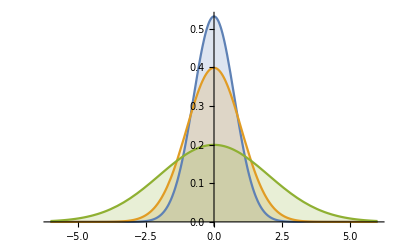

```mathematica
Plot[Table[PDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}]//Evaluate,{x,-6,6},Filling->Axis]
```

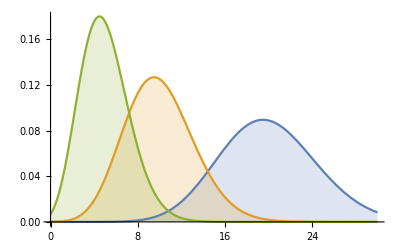

```mathematica
Plot[Table[PDF[PoissonDistribution[λ],k],{λ,{20,10,5}}]//Evaluate,{k,0,30},PlotRange->All,Filling->Axis]
```

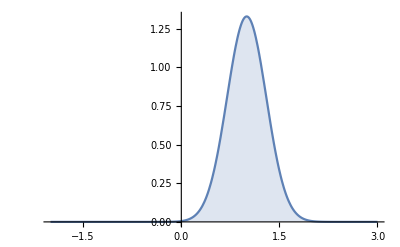

```mathematica
Plot[PDF[NormalDistribution[1,0.3],x],{x,-2,3},PlotRange->All,Filling->Axis]
```

#### Adding noise to intensity data

```mathematica
?intLCPolRet
```

```mathematica
(*raw data that represent intensity images with 10 by 10 pixels that result in zero retardance because the intensities of all 4 elliptical settings are equal, such as 100*)
data={Table[10,10,10],Table[100,10,10],Table[100,10,10],Table[100,10,10],Table[100,10,10]};
```

```mathematica
(*Adding noise to intensity data that are used to compute the retardance (ret) and orientation (azim) values*)
dataN={RandomVariate[PoissonDistribution[10],{10,10}],RandomVariate[PoissonDistribution[100],{10,10}],RandomVariate[PoissonDistribution[100],{10,10}],RandomVariate[PoissonDistribution[100],{10,10}],RandomVariate[PoissonDistribution[100],{10,10}]};
```

```mathematica
ret=intLCPolRet[dataN,0.05];
```

```mathematica
Min[ret]
```

0.00091817

```mathematica
Max[ret]
```

0.0440452

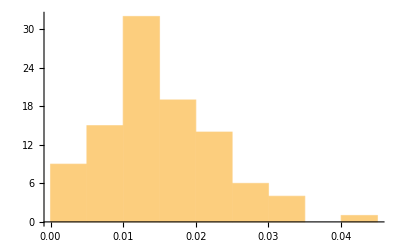

```mathematica
Histogram[Flatten[ret]]
```

```mathematica
azim=intLCPolAzim[dataN,0.05];
```

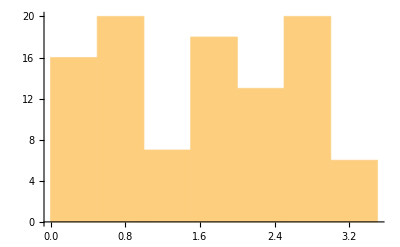

```mathematica
Histogram[Flatten[azim]]
```

Rays that accumulate zero retardance but whose intensities of the four elliptical settings are different due to shot noise, those rays (image pixels) evaluate to small retardance values (ret) that seem to have a Poisson distribution. The associated orientation (azim) data are uniformly distributed between zero and π radian.

```mathematica
?jMLCPolInt
```

```mathematica
?lRJM
```

```mathematica
ret=-0.03 2Pi;azim=-0.25 Pi;swing=0.05;dim=10;
dataI=100000{Table[jMLCPolInt[lRJM[ret,azim],0,0],dim,dim],Table[jMLCPolInt[lRJM[ret,azim],swing,0],dim,dim],Table[jMLCPolInt[lRJM[ret,azim],0,swing],dim,dim],Table[jMLCPolInt[lRJM[ret,azim],0,-swing],dim,dim],Table[jMLCPolInt[lRJM[ret,azim],-swing,0],dim,dim]};
dataN=Map[RandomVariate[PoissonDistribution[#]]&,dataI,{3}];
```

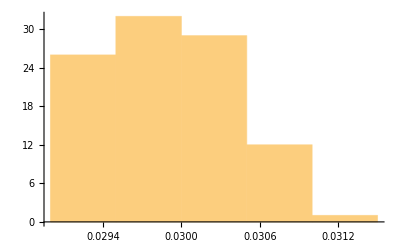

```mathematica
intLCPolRet[dataN,0.05]/(2Pi);
Histogram[Flatten[%]]
```

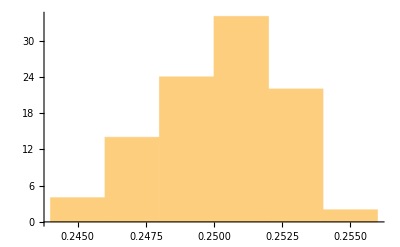

```mathematica
azim=intLCPolAzim[dataN,0.05]/(Pi);
Histogram[Flatten[%]]
```

#### Adding noise to retardance and orientation data

```mathematica
RandomVariate[NormalDistribution[0,0.1],{10,2}]
```

{{-0.0667042,0.0421618},{0.134478,0.0454285},{0.00703498,0.155362},{-0.0630982,0.0303718},{0.0310691,-0.106371},{-0.0843863,-0.0411625},{0.0188497,0.143172},{0.0246046,0.00175251},{-0.139649,0.0676219},{0.0170316,0.0774466}}

```mathematica
(*Adding noise to data*)
tmp1=guvBir[3,1,0.1];
dim1=tmp1[[3]]//Dimensions;
tmp1N=tmp1;
(*the next line adds noise to voxels that have birefringence other than zero*)
tmp1N[[2]]=tmp1[[2]]RandomVariate[NormalDistribution[1,0.1],{dim1[[1]],dim1[[2]],dim1[[3]]}];
(*the next line adds birefringence noise to all voxels that had initially zero birefringence*)
tmp1N[[2]]=Table[If[tmp1[[2,i,j,k]]==0,RandomVariate[NormalDistribution[0,0.001]],tmp1[[2,i,j,k]]],{i,dim1[[1]]},{j,dim1[[2]]},{k,dim1[[3]]}];(*the next line adds noise to the optic axis orientation of voxels that had originally non-zero birefringence*)
tmp1N[[3]]=Table[If[tmp1[[2,i,j,k]]≠0,(tmp1[[3,i,j,k]]+RandomVariate[NormalDistribution[0,0.2],3])//Normalize,{0,0,0}],{i,dim1[[1]]},{j,dim1[[2]]},{k,dim1[[3]]}];
(*the next line generates noisy optic axis orientations of voxels that had originally zero birefringence*)
tmp1N[[3]]=Table[If[tmp1[[2,i,j,k]]==0,RandomVariate[NormalDistribution[0,0.2],3]//Normalize,tmp1[[3,i,j,k]]],{i,dim1[[1]]},{j,dim1[[2]]},{k,dim1[[3]]}];
```

```mathematica
Point[Flatten[tmp1N[[3]],2]]//Graphics3D
```

-Graphics3D-

```mathematica
(*smp=guvBir[3,1,0.1];*)
smp=tmp1N;
Print@@smp[[1]];
Graphics3D[Raster3D[smp[[2]]/smp[[1,-1]],ColorFunction->"GrayLevelOpacity"],ImageSize->200]
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{Red,Map[Line,tmp]},ImageSize->300]
```

GUV box {X,Y,Z}={9,9,9}, GUV radius=3.5, membrane thick=1, all in units of voxPitch=0.577778µm, Δn=0.1

-Graphics3D-

-Graphics3D-

### Export objects as HDF5 files

Only at the point of export to HDF5 files are the object arrays, including the optic axis vector, rearranged to conform to the python code. 

Rotating the bundle by a negative theta value, such as -90°, makes the X-component of the optic axis vector positive, while a  theta rotation by a positive angle makes the X-component of the optic axis vector negative.

```mathematica
smp=bundleBir[2.5,7,-0.01,-45°,45°];
Print@@smp[[1]];
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{
FaceForm[],Cuboid[{0,0,0},smp[[1,2]]],Raster3D[smp[[2]]/smp[[1,8]],ColorFunction->"GrayLevelOpacity"],
Translate[{FaceForm[],Cuboid[{0,0,0},smp[[1,2]]],Red,Map[Line,tmp]},{9,0,0}],
Thick,Arrow[{{-2,-2,-2},{7,-2,-2}}],Text["X",{3.5,-4,-2}],Arrow[{{-2,-2,-2},{-2,7,-2}}],Text["Y",{-3,2,-2}],Arrow[{{-2,-2,-2},{-2,-2,7}}],Text["Z",{-3.5,-2,2}]},Boxed->False]
```

Bundle box {X,Y,Z}={9,9,9}, radius=2.5, length=7, all in units of voxPitch, birefringence=-0.01, rotation theta=-45 °, rotation azim=45 °

-Graphics3D-

#### bundle objects

```mathematica
bundleX={{{1,1,1},ballBir[0,0,0,0]},{{6,23,23},bundleBir[2.5,7,0.01,-90°,0°]},{{15,51,51},ballBir[0,0,0,0]}};
bundleXX={{{1,1,1},ballBir[0,0,0,0]},{{6,23,23},bundleBir[2.5,7,-0.01,-90°,0°]},{{15,51,51},ballBir[0,0,0,0]}};
bundleXXX={{{1,1,1},ballBir[0,0,0,0]},{{6,23,23},bundleBir[2.5,7,0.01,90°,0°]},{{15,51,51},ballBir[0,0,0,0]}};
bundleY={{{1,1,1},ballBir[0,0,0,0]},{{6,23,23},bundleBir[2.5,7,0.01,0°,0°]},{{15,51,51},ballBir[0,0,0,0]}};
bundleZ={{{1,1,1},ballBir[0,0,0,0]},{{6,23,23},bundleBir[2.5,7,0.01,0°,90°]},{{15,51,51},ballBir[0,0,0,0]}};
bundleZZ={{{1,1,1},ballBir[0,0,0,0]},{{6,23,23},bundleBir[2.5,7,-0.01,0°,90°]},{{15,51,51},ballBir[0,0,0,0]}};
bundleZZZ={{{1,1,1},ballBir[0,0,0,0]},{{6,23,23},bundleBir[2.5,7,0.01,0°,-90°]},{{15,51,51},ballBir[0,0,0,0]}};
bundleYZ={{{1,1,1},ballBir[0,0,0,0]},{{6,23,23},bundleBir[2.5,7,0.01,0°,45°]},{{15,51,51},ballBir[0,0,0,0]}};
bundleXYZ={{{1,1,1},ballBir[0,0,0,0]},{{6,23,23},bundleBir[2.5,7,0.01,-45°,45°]},{{15,51,51},ballBir[0,0,0,0]}};
```

```mathematica
(*Building a single object volume*)
smp=bundleZZZ;
smpDim=Table[smp[[i,2,2]]//Dimensions,{i,Length[smp]}];
SparseArray[Flatten[Table[Table[({k-1,j-1,i-1}+Reverse[smp[[n,1]]])->smp[[n,2,2,k,j,i]],{i,smpDim[[n,3]]},{j,smpDim[[n,2]]},{k,smpDim[[n,1]]}],{n,Length[smp]}]]];
SparseArray[Flatten[Table[Table[{({k-1,j-1,i-1,3}+Append[Reverse[smp[[n,1]]],0])->smp[[n,2,3,k,j,i,3]],({k-1,j-1,i-1,2}+Append[Reverse[smp[[n,1]]],0])->smp[[n,2,3,k,j,i,2]],({k-1,j-1,i-1,1}+Append[Reverse[smp[[n,1]]],0])->smp[[n,2,3,k,j,i,1]]},{i,smpDim[[n,3]]},{j,smpDim[[n,2]]},{k,smpDim[[n,1]]}],{n,Length[smp]}]]];
objVolBir={{"Object box {X,Y,Z}=",Reverse[Dimensions[%%]],", in units of voxPitch"},%%,%};
```

```mathematica
(*Graphics for larger object volume*)
smp=objVolBir;
Print@@smp[[1]];
ΔnMax=Max[Abs[smp[[2]]]];
Graphics3D[Raster3D[Abs[smp[[2]]]/(ΔnMax),ColorFunction->"GrayLevelOpacity"],Axes->True,AxesLabel->{"X","Y","Z"}]
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{Red,Map[Line,tmp]},ImageSize->300]
```

Object box {X,Y,Z}={15,51,51}, in units of voxPitch

-Graphics3D-

-Graphics3D-

```mathematica
optInfoDescript="Object box {X,Y,Z}="<>ToString[smp[[1,2]]]<>", bundleBir[radius=2.5,length=7,Δn=0.01,theta=0°,azim=-90°] -> bundleZZZ, optic axis given as unit vector {X,Y,Z}";
Print[optInfoDescript];
```

Object box {X,Y,Z}={15, 51, 51}, bundleBir[radius=2.5,length=7,Δn=0.01,theta=0°,azim=-90°] -> bundleZZZ, optic axis given as unit vector {X,Y,Z}

```mathematica
SetDirectory["/Users/rudolfo/Software/GitHub/forward-model/objects"];
```

```mathematica
Export["bundleZZZ.h5",{
"optical_info/description"->optInfoDescript,
"optical_info/volume_shape"->smp[[1,2]],
"data/delta_n"->Transpose[smp[[2]],{3,2,1}]//Normal,
"data/optic_axis"->Transpose[smp[[3]],{4,3,2,1}]//Normal
}]
```

bundleZZZ.h5

```mathematica
Import["bundleX.h5","StructureGraph"]
```

-Graphics-

```mathematica
Import["bundleX.h5","optical_info/description"]
```

Object box {X,Y,Z}={15, 51, 51}, bundleBir[radius=2.5,length=7,Δn=0.01,theta=-90°,azim=0°] -> bundleX, optic axis given as unit vector {X,Y,Z}

```mathematica
Import["bundleX.h5","data/optic_axis"]//Dimensions
```

{3,15,51,51}

#### shell objects

```mathematica
voxPitch=0.578;  (*µm, used for shellBir[]*)
smp=shellBir[120,117,{2,0,0},35,-0.172];  (*shell_JOSAA2022.h5*)
```

```mathematica
Print@@smp[[1]]
```

Shell box {X,Y,Z}={38,243,243}, shell outer radius=120.5, shell inner radius=117.5, radius center displacement={2,0,0}, shell height=35, all in units of voxPitch=0.578µm, Δn=-0.172

```mathematica
narrative="This shell object was used in the simulation published in article by Ruiz and Oldenbourg, JOSAA  2022,";
optInfoDescript=StringTrim[StringReplace[TextString[Drop[Drop[smp[[1]],2],-7]],{"=, "->"=",", ,"->","}],{"{","}"}];
optInfoDescript=narrative<>"\nshell array dimensions {Z,Y,X}="<>ToString[Reverse[smp[[1,2]]]]<>optInfoDescript<>ToString[Reverse[smp[[1,8]]]];
optInfoDescript=optInfoDescript<>smp[[1,9]]<>ToString[smp[[1,10]]]<>", all in units of voxPitch="<>ToString[voxPitch]<>"µm, birefringence="<>ToString[smp[[1,-1]]]<>", optic axis given as unit vector {Z,Y,X}";
Print[optInfoDescript];
```

This shell object was used in the simulation published in article by Ruiz and Oldenbourg, JOSAA  2022,
shell array dimensions {Z,Y,X}={243, 243, 38}, shell outer radius=120.5, shell inner radius=117.5, radius center displacement={0, 0, 2}, shell height=35, all in units of voxPitch=0.578µm, birefringence=-0.172, optic axis given as unit vector {Z,Y,X}

```mathematica
Export["shell_JOSAA2022.h5",{
"optical_info/description"->optInfoDescript,
"optical_info/volume_shape"->smp[[1,2]],
"data/delta_n"->Transpose[smp[[2]],{3,2,1}]//Normal,
"data/optic_axis"->Transpose[smp[[3]],{4,3,2,1}]//Normal
}]
```

shell_JOSAA2022.h5

#### guv objects

```mathematica
?guvBir
```

```mathematica
(*For generating guv1 and guv2*)
Transpose[{guvBir[3.5,1,-0.1][[2,All,All,5]]},{3,1,2}];
Transpose[{guvBir[3.5,1,-0.1][[3,All,All,5]]},{3,1,2}];
objVolBir={{"Object box {X,Y,Z}=",Reverse[Dimensions[%%]],", in units of voxPitch"},%%,%};
```

```mathematica
objVolBir[[2]]//Dimensions
```

{9,9,1}

```mathematica
guv1={{{1,1,1},ballBir[0,0,0,0]},{{8,27,27},objVolBir},{{15,61,61},ballBir[0,0,0,0]}};
```

```mathematica
guv2={{{1,1,1},ballBir[0,0,0,0]},{{8,27,27},objVolBir},{{15,61,61},ballBir[0,0,0,0]}};
```

```mathematica
guv3={{{1,1,1},ballBir[0,0,0,0]},{{1,24,24},guvBir[6.5,1,0.01]},{{15,61,61},ballBir[0,0,0,0]}};
```

```mathematica
guv4={{{1,1,1},ballBir[0,0,0,0]},{{1,36,36},guvBir[9.5,1,0.01]},{{23,91,91},ballBir[0,0,0,0]}};
```

```mathematica
guv5={{{1,1,1},ballBir[0,0,0,0]},{{4,38,38},guvBir[7.5,1,0.002]},{{23,91,91},ballBir[0,0,0,0]}};
```

```mathematica
random1={{{1,1,1},ballBir[0,0,0,0]},{{23,91,91},ballBir[0,0,0,0]}};
```

```mathematica
random2={{{1,1,1},ballBir[0,0,0,0]},{{15,61,61},ballBir[0,0,0,0]}};
```

```mathematica
(*Building a single object volume*)
smp=guv3;
smpDim=Table[smp[[i,2,2]]//Dimensions,{i,Length[smp]}];
SparseArray[Flatten[Table[Table[({k-1,j-1,i-1}+Reverse[smp[[n,1]]])->smp[[n,2,2,k,j,i]],{i,smpDim[[n,3]]},{j,smpDim[[n,2]]},{k,smpDim[[n,1]]}],{n,Length[smp]}]]];
SparseArray[Flatten[Table[Table[{({k-1,j-1,i-1,3}+Append[Reverse[smp[[n,1]]],0])->smp[[n,2,3,k,j,i,3]],({k-1,j-1,i-1,2}+Append[Reverse[smp[[n,1]]],0])->smp[[n,2,3,k,j,i,2]],({k-1,j-1,i-1,1}+Append[Reverse[smp[[n,1]]],0])->smp[[n,2,3,k,j,i,1]]},{i,smpDim[[n,3]]},{j,smpDim[[n,2]]},{k,smpDim[[n,1]]}],{n,Length[smp]}]]];
objVolBir={{"Object box {X,Y,Z}=",Reverse[Dimensions[%%]],", in units of voxPitch"},%%,%};
```

```mathematica
(*guv3*)
objVolBir[[2,31-15;;31+15,31-15;;31+15,8]]//Image//ImageAdjust
```

-Graphics-

```mathematica
(*guv4*)
objVolBir[[2,46-15;;46+15,46-15;;46+15,12]]//Image//ImageAdjust
```

-Graphics-

```mathematica
(*Adding noise to data*)
tmp1=objVolBir;
dim1=tmp1[[3]]//Dimensions;
tmp1N=tmp1;
(*the next line adds noise to voxels that have birefringence other than zero*)
tmp1N[[2]]=tmp1N[[2]]RandomVariate[NormalDistribution[1,0.1],{dim1[[1]],dim1[[2]],dim1[[3]]}];
(*the next line adds birefringence noise to all voxels that had initially zero birefringence*)
tmp1N[[2]]=Table[If[tmp1N[[2,i,j,k]]==0,0.0001RandomVariate[PoissonDistribution[20]],tmp1N[[2,i,j,k]]],{i,dim1[[1]]},{j,dim1[[2]]},{k,dim1[[3]]}];(*the next line adds noise to the optic axis orientation of voxels that had originally non-zero birefringence*)
tmp1N[[3]]=Table[If[tmp1N[[2,i,j,k]]≠0,(tmp1N[[3,i,j,k]]+RandomVariate[NormalDistribution[0,0.2],3])//Normalize,{0,0,0}],{i,dim1[[1]]},{j,dim1[[2]]},{k,dim1[[3]]}];
(*the next line generates noisy optic axis orientations of voxels that had originally zero birefringence*)
tmp1N[[3]]=Table[If[tmp1[[2,i,j,k]]==0,RandomVariate[NormalDistribution[0,0.2],3]//Normalize,tmp1[[3,i,j,k]]],{i,dim1[[1]]},{j,dim1[[2]]},{k,dim1[[3]]}];
```

```mathematica
Min[tmp1N[[2]]]
```

5.17224×10^-6

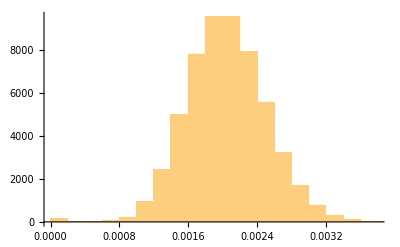

```mathematica
Flatten[tmp1N[[2]]]//Histogram
```

```mathematica
Point[Flatten[tmp1N[[3]],2][[5000;;10000]]]//Normal//Graphics3D
```

-Graphics3D-

```mathematica
Map[Norm,tmp1N[[3]],{3}]//Min
```

1.

```mathematica
(*smp=objVolBir;*)
smp=tmp1N;
Print@@smp[[1]];
ΔnMax=Max[Abs[smp[[2]]]];
Graphics3D[Raster3D[Abs[smp[[2]]]/(ΔnMax),ColorFunction->"GrayLevelOpacity"],Axes->True,AxesLabel->{"X","Y","Z"}(*,ImageSize->100*)]
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{Red,Map[Line,tmp]}(*,ImageSize->100*)]
```

Object box {X,Y,Z}={15,61,61}, in units of voxPitch

-Graphics3D-

-Graphics3D-

```mathematica
optInfoDescript="Object box {X,Y,Z}="<>ToString[smp[[1,2]]]<>","<>"\nrandom2 -> random birefringence values and optic axis orientations.";
Print[optInfoDescript];
```

Object box {X,Y,Z}={15, 61, 61},
random2 -> random birefringence values and optic axis orientations.

```mathematica
optInfoDescript="Object box {X,Y,Z}="<>ToString[smp[[1,2]]]<>","<>"\nguv5_GT -> guvBir[radius=7.5,membrane thickness=1,Δn=0.002], optic axis given as unit vector {X,Y,Z},"<>"\nGT stands for ground truth.";
Print[optInfoDescript];
```

Object box {X,Y,Z}={23, 91, 91},
guv5_GT -> guvBir[radius=7.5,membrane thickness=1,Δn=0.002], optic axis given as unit vector {X,Y,Z},
GT stands for ground truth.

```mathematica
optInfoDescript="Object box {X,Y,Z}="<>ToString[smp[[1,2]]]<>","<>"\nguv3N2_GT -> guvBir[radius=9.5,membrane thickness=1,Δn=0.01], optic axis given as unit vector {X,Y,Z},"<>"\nGT stands for ground truth, N stands for noise added to data.";
Print[optInfoDescript];
```

Object box {X,Y,Z}={15, 61, 61},
guv3N2_GT -> guvBir[radius=9.5,membrane thickness=1,Δn=0.01], optic axis given as unit vector {X,Y,Z},
GT stands for ground truth, N stands for noise added to data.

```mathematica
SetDirectory["/Users/rudolfo/Software/GitHub/forward-model/objects/GUVs"];
```

```mathematica
SetDirectory["/Users/rudolfo/Desktop"];
```

```mathematica
Export["guv3N2_GT.h5",{
"optical_info/description"->optInfoDescript,
"optical_info/volume_shape"->smp[[1,2]],
"data/delta_n"->Transpose[smp[[2]],{3,2,1}]//Normal,
"data/optic_axis"->Transpose[smp[[3]],{4,3,2,1}]//Normal
}]
```

guv3N2_GT.h5

```mathematica
Import["guv4_Recon2_forwardRetStream.tiff","MetaInformation"]
```

<|Exif→<|ImageWidth→289,ImageLength→289,BitsPerSample→32,Compression→Uncompressed,PhotometricInterpretation→BlackIsZero,ImageDescription→{"Description": "forward projection of .../GitHub/forward-model/objects/GUVs/guv4_Recon2.h5", "Comments": "", "Optical info": {"volume_shape": [23, 91, 91], "axial_voxel_size_um": 1.0, "cube_voxels": true, "pixels_per_ml": 17, "n_micro_lenses": 17, "n_voxels_per_ml": 3, "M_obj": 60, "na_obj": 1.2, "n_medium": 1.35, "wavelength": 0.55, "camera_pix_pitch": 6.5, "voxel_size_um": [1.8416666666666666, 1.8416666666666666, 1.8416666666666666]}, "Streamlit parameters": {"medium_option": "Water: n = 1.35", "backend_choice": "numpy", "how_get_vol": "h5 upload", "vol_shape_default": [23, 91, 91], "display_h5": false, "azimuth_plot_type": "hsv", "current_date": "2023-07-13", "default_directory": "forward_results/2023-07-13", "save_directory": "forward_results/2023-07-12"}, "shape": [289, 289]},StripOffsets→1040,SamplesPerPixel→1,RowsPerStrip→289,StripByteCounts→334084,XResolution→1,YResolution→1,ResolutionUnit→None,Software→tifffile.py,SampleFormat→3|>|>

```mathematica
fileName="guv5N1_GT";
Import[fileName<>".h5","StructureGraph"]
```

-Graphics-

```mathematica
(tmp=Import[fileName<>".h5","data/delta_n"])//Dimensions
```

{23,91,91}

```mathematica
Max[tmp]
```

0.00467371

```mathematica
smp=Import[fileName<>".h5","optical_info/description"];
If[smp=={"Temporary description"},smp={fileName<>".h5 "}];
smp=Append[{smp},Import[fileName<>".h5","data/delta_n"]//Dimensions];
smp={smp,Transpose[Import[fileName<>".h5","data/delta_n"],{3,2,1}]};
smp=Append[smp,Transpose[Import[fileName<>".h5","data/optic_axis"],{4,3,2,1}]];
Δn=If[Max[smp[[2]]]==0,Min[smp[[2]]],Max[smp[[2]]]];
```

```mathematica
Print@smp[[1]]
```

{{guv3_Recon1.h5 },{15,61,61}}

```mathematica
Δn
```

0.0265015

```mathematica
(*smp=bundleBir[2.5,7,-0.01,0°,15°];Δn=If[smp[[1,8]]<0,Min[smp[[2]]],Max[smp[[2]]]];*)
Print@smp[[1]];
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{
FaceForm[],Cuboid[{0,0,0},smp[[1,2]]],Raster3D[smp[[2]]/Δn,ColorFunction->"GrayLevelOpacity"],
Translate[{FaceForm[],Cuboid[{0,0,0},smp[[1,2]]],Red,Map[Line,tmp]},{40,0,0}],
Thick,Arrow[{{-2,-2,-2},{7,-2,-2}}],Text["StyleBox[\"X\",FontWeight->\"Bold\"]",{3.5,-4,-2}],Arrow[{{-2,-2,-2},{-2,7,-2}}],Text["StyleBox[\"Y\",FontWeight->\"Bold\"]",{-3,2,-2}],Arrow[{{-2,-2,-2},{-2,-2,7}}],Text["StyleBox[\"Z\",FontWeight->\"Bold\"]",{-3.5,-2,2}]},Boxed->False]
```

{{guv3_Recon1.h5 },{15,61,61}}

-Graphics3D-

```mathematica
smp=bundleBir[2.5,7,-0.01,-45°,45°];
Print@@smp[[1]];
tmp=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Graphics3D[{
FaceForm[],Cuboid[{0,0,0},smp[[1,2]]],Raster3D[smp[[2]]/smp[[1,8]],ColorFunction->"GrayLevelOpacity"],
Translate[{FaceForm[],Cuboid[{0,0,0},smp[[1,2]]],Red,Map[Line,tmp]},{9,0,0}],
Thick,Arrow[{{-2,-2,-2},{7,-2,-2}}],Text["StyleBox[\"X\",FontWeight->\"Bold\"]",{3.5,-4,-2}],Arrow[{{-2,-2,-2},{-2,7,-2}}],Text["StyleBox[\"Y\",FontWeight->\"Bold\"]",{-3,2,-2}],Arrow[{{-2,-2,-2},{-2,-2,7}}],Text["StyleBox[\"Z\",FontWeight->\"Bold\"]",{-3.5,-2,2}]},Boxed->False]
```

```mathematica
(*end*)
```

#### single voxel scans

```mathematica
voxScan=Table[{"voxelScanΔn1m2OA100X"<>If[i<0,"m"<>ToString[Abs[i]],ToString[i]]<>"Ym1Zm1",toObjVolBir[{{{8+i,25,25},ballBir[0,0.01,0,0]},{{1,1,1},ballBir[0,0,0,0]},{{15,51,51},ballBir[0,0,0,0]}}]},{i,-7,7}];
```

```mathematica
voxScan//Dimensions
```

{15,2}

```mathematica
voxScan[[1,1]]
```

voxelScanΔn1m2OA100Xm7Ym1Zm1

```mathematica
optInfoDescript="Object box {X,Y,Z}="<>ToString[voxScan[[1,2,1,2]]]<>", single voxel ballBir[0,0.01,0,0], optic axis given as unit vector {X,Y,Z}";
Print[optInfoDescript];
```

Object box {X,Y,Z}={15, 51, 51}, single voxel ballBir[0,0.01,0,0], optic axis given as unit vector {X,Y,Z}

```mathematica
SetDirectory["/Users/rudolfo/Software/GitHub/forward-model/objects/SingleVoxelScans/voxelScanVolH5Files"];
```

```mathematica
Do[Export[voxScan[[i,1]]<>".h5",{
"optical_info/description"->optInfoDescript,
"optical_info/volume_shape"->voxScan[[i,2,1,2]],
"data/delta_n"->Transpose[voxScan[[i,2,2]],{3,2,1}],
"data/optic_axis"->Transpose[voxScan[[i,2,3]],{4,3,2,1}]
}],{i,Dimensions[voxScan][[1]]}]
```

### Import objects as HDF5 files

```mathematica
SetDirectory["/Users/rudolfo/Software/GitHub/forward-model/objects/GUVs/"];
```

```mathematica
fileName="guv3N2_GT";
```

```mathematica
description={Import[fileName<>".h5","optical_info/description"],Import[fileName<>".h5","data/delta_n"]//Dimensions}
```

{Object box {X,Y,Z}={15, 61, 61},
guv3N2_GT -> guvBir[radius=9.5,membrane thickness=1,Δn=0.01], optic axis given as unit vector {X,Y,Z},
GT stands for ground truth, N stands for noise added to data.,{15,61,61}}

```mathematica
Import[fileName<>".h5","StructureGraph"]
```

-Graphics-

```mathematica
(Δn=Transpose[Import[fileName<>".h5","data/delta_n"],{3,2,1}])//Dimensions
```

{61,61,15}

```mathematica
(oA=Transpose[Import[fileName<>".h5","data/optic_axis"],{4,3,2,1}])//Dimensions
```

{61,61,15,3}

```mathematica
Min[Δn]
```

5.17224×10^-6

```mathematica
Map[Norm,oA,{3}]//Min
```

1.

```mathematica
Point[Flatten[oA,2][[500;;5000]]]//Graphics3D
```

-Graphics3D-

```mathematica
Max[Δn]
```

0.0113774

```mathematica
smp={description,Δn,oA};threshold=0.005;
Print@@smp[[1]];
tmp=Flatten[Table[If[Abs[Δn[[k,j,i]]]>threshold,{{i-0.5,j-0.5,k-0.5}-smp[[3,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[3,k,j,i]]/2},{{i-0.5,j-0.5,k-0.5}-0,{i-0.5,j-0.5,k-0.5}+0}],
			{i,smp[[1,2,1]]},{j,smp[[1,2,2]]},{k,smp[[1,2,3]]}],2];
Row[{Graphics3D[Raster3D[0.9smp[[2]]/Max[Δn],ColorFunction->"GrayLevelOpacity"],ImageSize->400],
Graphics3D[{Red,Map[Line,tmp]},ImageSize->400]}]
```

Object box {X,Y,Z}={15, 61, 61},
guv3N2_GT -> guvBir[radius=9.5,membrane thickness=1,Δn=0.01], optic axis given as unit vector {X,Y,Z},
GT stands for ground truth, N stands for noise added to data.{15,61,61}

-Graphics3D--Graphics3D-

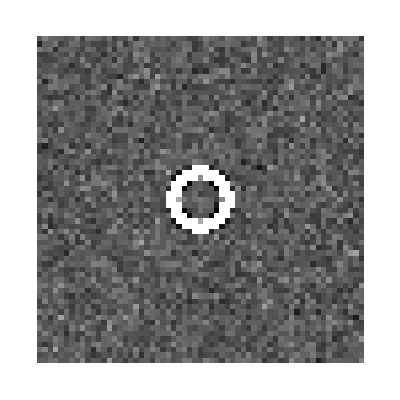

```mathematica
Graphics[Raster[10smp[[2,All,All,11]]/Max[Δn]],ImageSize->400]
```

```mathematica
Import["/Users/rudolfo/Software/GitHub/forward-model/objects/single_voxel.h5","optical_info/description"]
```

{Shell created from a section of an ellipsoid with an optic axis normal to the                   surface of the shell.}

```mathematica
Import["shell_JOSAA2022.h5","optical_info/description"]
```

This shell object was used in the simulation published in article by Ruiz and Oldenbourg, JOSAA  2022,
shell array dimensions {Z,Y,X}={243, 243, 38}, shell outer radius=120.5, shell inner radius=117.5, radius center displacement={0, 0, 2}, shell height=35, all in units of voxPitch=0.578µm, birefringence=-0.172, optic axis given as unit vector {Z,Y,X}

### Graphics for light field camera, object space, a complete Light Field LC-PolScope

#### Initialization

```mathematica
voxPitchGraphics=25;        (*voxel size for rendering graphics; it is typically much bigger than the simulation voxPitch*)
voxPitchGraphicsList={voxPitchGraphics,voxPitchGraphics,voxPitchGraphics};
If[OddQ[voxNrXGraphics=Round[250/voxPitchGraphics]],,voxNrXGraphics=voxNrXGraphics+1]; (*voxNrXGraphics is the number of voxels along the x-axis side of the object cube. An odd number will put the Center of a voxel in the center of object space*)
If[OddQ[voxNrYZGraphics=Round[700/voxPitchGraphics]],,voxNrYZGraphics=voxNrYZGraphics+1]; (*voxNrYZGraphics is the number of voxels along the y- and z-axis side of the object cube An odd number will put the Center of a voxel in the center of object space*)
voxNrCtrGraphics={voxNrXGraphics/2,voxNrYZGraphics/2,voxNrYZGraphics/2};(*voxNrCtrGraphics is the number location in object space on which all camera rays converge*)
volCtrGraphics={voxNrXGraphics*voxPitchGraphics/2,voxNrYZGraphics*voxPitchGraphics/2,voxNrYZGraphics*voxPitchGraphics/2};(*volCtr is the center of the sample volume and the location in object space on which all rays of the central microlens converge*)

voxPitch=µLensPitch/5;voxPitch::usage="voxPitch is the side length in micron of a cubic voxel in object space;\nyou can change it to voxPitch=µLensPitch/1, or voxPitch=µLensPitch/3, voxPitch=µLensPitch/5";
λ=0.550; wavelength::usage="λ is the wavelength in µm of light propagating through the sample volume.\nIt is used to convert retardance given as Δn times the ray's path length into a phase angle and vice versa";
If[OddQ[voxNrX=Round[250/voxPitch]],,voxNrX=voxNrX+1]; voxNrX::usage="voxNrX is the number of voxels along the x-axis side of the object cube.\nAn odd number will put the Center of a voxel in the center of object space";
If[OddQ[voxNrYZ=Round[700/voxPitch]],,voxNrYZ=voxNrYZ+1]; voxNrYZ::usage="voxNrYZ is the number of voxels along the y- and z-axis side of the object cube\nAn odd number will put the Center of a voxel in the center of object space";
voxNrCtr={voxNrX/2,voxNrYZ/2,voxNrYZ/2};voxNrCtr::usage="voxNrCtr is the number location in object space on which all camera rays converge";
volCtr={voxNrX*voxPitch/2,voxNrYZ*voxPitch/2,voxNrYZ*voxPitch/2};volCtr::usage="volCtr is the center of the sample volume in µm and the location in object space on which all rays of the central microlens converge";
magnObj=60;  magnObj::usage="magnObj is the magnification of objective lens";
µLensCtr={8,8}; µLensCtr::usage="µLensCtr is the microLens center position in camera pixels";
µLensPitch=nrCamPix*camPixPitch/magnObj;  µLensPitch::usage="µLens pitch in object space is about 1.733µm when using 60x objective lens.\n1.733*60=104µm is actually a bit bigger than 100µm pitch of the experimental µLens array.\n104µm makes it an integer number of camera pixels.";
rNA =7.5;  rNA::usage="rNA is the radius of the edge of the objective lens aperture in camera pixels; rNA = 7.5 for 60x/1.4NA objective lens and a condenser NA of 1.2";
nrCamPix=16;  nrCamPix::usage="nrCamPix is the number of camera pixels behind a lenslet in the horizontal and vertical direction\n0≤i≤nrCamPix and 0≤j≤nrCamPix span the plane of camera pixels, with {i,j} Reals\nIntegers {i,j} count the pixels. {0.5,0.5} is the center location of pixel {1,1}";
camPixPitch=6.5;  camPixPitch::usage="camPixPitch is the size of the camera pixels in µm in image space";
naObj=1.2;     naObj::usage="naObj is NA of objective lens";
nMedium=1.52;  nMedium::usage="nMedium is the refractive index of the medium in object space";

(*The computation implements the Abbe sine condition for points in the back focal plane of the objective lens*)
(*Making this a delayed assignment slows down the computation tremendously*)
(*Angle values need to be converted and rounded to integer degrees, otherwise later the test for all members of mP and iL having equal length fails for all voxPitch values. I don't know why!*)
camPixRays::usage="The list camPixRays[[i,j]] holds values for azimuth and tilt angles in object space for rays originating in camera pixels {i,j} behind the central lenslet";
camPixRays=Table[If[(tmp=Sqrt[(i-0.5-µLensCtr[[1]])^2+(j-0.5-µLensCtr[[2]])^2])>rNA,{Null},
	{ArcTan[i-0.5-µLensCtr[[1]],j-0.5-µLensCtr[[2]]]/Degree,ArcSin[tmp/rNA*naObj/nMedium]/Degree}//Round],{i,nrCamPix},{j,nrCamPix}];

(*2D line grid representing camera pixel array behind one microlens*)
camPixels2D:={
	Table[Line[{{1,0}*i,{1,0}*i+{0,1}*nrCamPix}],{i,0,nrCamPix}],
	Table[Line[{{0,1}*i,{0,1}*i+{1,0}*nrCamPix}],{i,0,nrCamPix}],
	Table[Text[{i,j},{(i-0.5),(j-0.5)}],{i,nrCamPix},{j,nrCamPix}]
}

camRayEntrance::usage="The camRayEntrance list holds the positions where camera rays originating in pixel {i,j} pass through the entrance face into the object cube.\nThe x position of the entrance face is 0, camera rays all converge on volCtr";
camRayEntrance:=Flatten[Table[If[camPixRays[[i,j]]=={Null},,{{i,j},
		{0,volCtr[[1]]*Tan[camPixRays[[i,j,2]]Degree]Sin[camPixRays[[i,j,1]]Degree]+volCtr[[2]],
		volCtr[[1]]*Tan[camPixRays[[i,j,2]]Degree]Cos[camPixRays[[i,j,1]]Degree]+volCtr[[3]]}}],{i,nrCamPix},{j,nrCamPix}]//N,1]//DeleteCases[Null]

nrRays=Length[camRayEntrance]; nrRays::usage="nrRays is the  number of all rays (172 for naObj=1.2 and rNA=7.5; 188 for naObj=1.2 and rNA=7.7) that fall onto the camera and pass through the objective aperture";

rayEnter::usage="List of object space coordinates where rays enter object space. The x-position is 0";
rayEnter=Table[camRayEntrance[[i,2]],{i,nrRays}];

rayExit::usage="List of object space coordinates where rays exit object space. The x-position is voxPitch*voxNrX";
rayExit=Table[rayEnter[[i]]+2(volCtr-rayEnter[[i]]),{i,nrRays}];

(*The camRayEntrance list holds the positions where camera rays originating in pixel {i,j} pass through the entrance face into the object cube or vice versa.\nThe x position of the entrance face is 0, camera rays all converge on volCtr*)
camRayEntranceGraphics::usage="The camRayEntranceGraphics list holds the positions where camera rays originating in pixel {i,j} pass through the entrance face into the object cube or vice versa.\nThe x position of the entrance face is 0, camera rays all converge on volCtr.\nDistances computed with Graphicsics related units (voxPitchGraphics, volCtrGraphics)";
camRayEntranceGraphics:=Flatten[Table[If[camPixRays[[i,j]]=={Null},,{{i,j},
		{0,volCtrGraphics[[1]]*Tan[camPixRays[[i,j,2]]Degree]Sin[camPixRays[[i,j,1]]Degree]+volCtrGraphics[[2]],
		volCtrGraphics[[1]]*Tan[camPixRays[[i,j,2]]Degree]Cos[camPixRays[[i,j,1]]Degree]+volCtrGraphics[[3]]}}],{i,nrCamPix},{j,nrCamPix}]//N,1]//DeleteCases[Null]

(*The entrance face is where rays enter object space. The face is in the y-z plane at x=0.\nDistances computed with Graphics related units (voxPitchGraphics,voxNrYZGraphics)*)
entranceFaceGraphics:={
	Table[Line[{{0,1,0}*voxPitchGraphics*i,{0,1,0}*voxPitchGraphics*i+{0,0,1}*voxPitchGraphics*voxNrYZGraphics}],{i,0,voxNrYZGraphics}],
	Table[Line[{{0,0,1}*voxPitchGraphics*i,{0,0,1}*voxPitchGraphics*i+{0,1,0}*voxPitchGraphics*voxNrYZGraphics}],{i,0,voxNrYZGraphics}]
}

(*2D line grid representing entrance face of rays that traverse object space.\nDistances computed with Graphics related units (voxPitchGraphics,voxNrYZGraphics)*)
entranceFace2DGraphics:={
	Table[Line[{{1,0}*voxPitchGraphics*i,{1,0}*voxPitchGraphics*i+{0,1}*voxPitchGraphics*voxNrYZGraphics}],{i,0,voxNrYZGraphics}],
	Table[Line[{{0,1}*voxPitchGraphics*i,{0,1}*voxPitchGraphics*i+{1,0}*voxPitchGraphics*voxNrYZGraphics}],{i,0,voxNrYZGraphics}]
}

(*The exit face is where rays exit object space. The face is in the y-z plane at x=voxNrXGraphics·voxPitchGraph*)
exitFaceGraphics:={
	Table[Line[{{0,1,0}*voxPitchGraphics*i+{1,0,0}*voxPitchGraphics*voxNrXGraphics,{0,1,0}*voxPitchGraphics*i+{0,0,1}*voxPitchGraphics*voxNrYZGraphics+{1,0,0}*voxPitchGraphics*voxNrXGraphics}],{i,0,voxNrYZGraphics}],
	Table[Line[{{0,0,1}*voxPitchGraphics*i+{1,0,0}*voxPitchGraphics*voxNrXGraphics,{0,0,1}*voxPitchGraphics*i+{0,1,0}*voxPitchGraphics*voxNrYZGraphics+{1,0,0}*voxPitchGraphics*voxNrXGraphics}],{i,0,voxNrYZGraphics}]
}

(*object cube.\nDistances computed with Graphics related units (voxPitchGraphics,voxNrxGraphics,voxNrYZGraphics)*)
objectCubeGraphics:={
	Table[Line[{{0,1,0}*voxPitchGraphics*i+{1,0,0}*voxPitchGraphics*j,{0,1,0}*voxPitchGraphics*i+{0,0,1}*voxPitchGraphics*voxNrYZGraphics+{1,0,0}*voxPitchGraphics*j}],{i,0,voxNrYZGraphics},{j,voxNrXGraphics-1}],
	Table[Line[{{0,0,1}*voxPitchGraphics*i+{1,0,0}*voxPitchGraphics*j,{0,0,1}*voxPitchGraphics*i+{0,1,0}*voxPitchGraphics*voxNrYZGraphics+{1,0,0}*voxPitchGraphics*j}],{i,0,voxNrYZGraphics},{j,voxNrXGraphics-1}],
	Table[Line[{{0,0,1}*voxPitchGraphics*i+{0,1,0}*voxPitchGraphics*j,{0,0,1}*voxPitchGraphics*i+{0,1,0}*voxPitchGraphics*j+{1,0,0}*voxPitchGraphics*voxNrXGraphics}],{i,0,voxNrYZGraphics},{j,0,voxNrYZGraphics}]
}

(*Siddon algorithms, Mathematica implementation by Rudolf Oldenbourg, March 2019, based on Python code from Nathaniel Holderman, UChicago, in 2018*)
(*pixNumXIn is the number of voxels in x-direction between entrance face and front face of bounding object box. The same applies to y- and z-direction*)
(*pixNumXOut is the number of voxels in x-direction between entrance face and back face of bounding object box. The same applies to y- and z-direction*)
(*dx_,dy_, and dz_ must be Real numbers, not integers*)
rayTrace[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
(*Catch[*)Module[{ax={},ax0,axN,ay={},ay0,ayN,az={},az0,azN,aMin,aMax,iMin,iMax,jMin,jMax,kMin,kMax},
(*first,compute starting and ending parametric values in each dimension*)
		If[x2-x1≠0,ax0=(pixNumXIn dx-x1)/(x2-x1);axN=(pixNumXOut*dx-x1)/(x2-x1),ax0=0.;axN=1.];
		If[y2-y1≠0,ay0=(pixNumYIn dy-y1)/(y2-y1);ayN=(pixNumYOut*dy-y1)/(y2-y1),ay0=0.;ayN=1.];
		If[z2-z1≠0,az0=(pixNumZIn dz-z1)/(z2-z1);azN=(pixNumZOut*dz-z1)/(z2-z1),az0=0.;azN=1.];
(*Print["ax0=",ax0,", axN=",axN,", ay0=",ay0,", ayN=",ayN,", az0=",az0,", azN=",azN];*)
(*then calculate absolute max and min parametric values*)
		aMin=Max[0.,Min[ax0,axN],Min[ay0,ayN],Min[az0,azN]];
		aMax=Min[1.,Max[ax0,axN],Max[ay0,ayN],Max[az0,azN]];
(*Print["aMin=",aMin,", aMax=",aMax];*)
(*now find range of indices corresponding to max/min a values*)
(*in this application, (x2-x1) is always greater zero*)
(*		iMin=Ceiling[(aMin*(x2-x1)-x1)/dx];iMax=Floor[1+(x1+aMax*(x2-x1))/dx];*)
		iMin=Ceiling[pixNumXOut-(pixNumXOut*dx-aMin*(x2-x1)-x1)/dx];iMax=Floor[1+(x1+aMax*(x2-x1))/dx];
		If[(y2-y1)≥0,
			jMin=Ceiling[pixNumYOut-(pixNumYOut*dy-aMin*(y2-y1)-y1)/dy];jMax=Floor[1+(y1+aMax*(y2-y1))/dy],
			jMin=Ceiling[pixNumYOut-(pixNumYOut*dy-aMax*(y2-y1)-y1)/dy];jMax=Floor[1+(y1+aMin*(y2-y1))/dy]];
		If[(z2-z1)≥0,
			kMin=Ceiling[pixNumZOut-(pixNumZOut*dz-aMin*(z2-z1)-z1)/dz];kMax=Floor[1+(z1+aMax*(z2-z1))/dz],
			kMin=Ceiling[pixNumZOut-(pixNumZOut*dz-aMax*(z2-z1)-z1)/dz];kMax=Floor[1+(z1+aMin*(z2-z1))/dz]];
(*Print["iMin=",iMin,", iMax=",iMax,", jMin=",jMin,", jMax=",jMax,", kMin=",kMin,", kMax=",kMax];*)
(*next calculate the list of parametric values for each coordinate*)
		For [i=iMin,i<iMax,i++,ax=Append[ax,(i*dx-x1)/(x2-x1)]];
		If [y2-y1>0,For [j=jMin,j<jMax,j++,ay=Append[ay,(j*dy-y1)/(y2-y1)]]];
		If [y2-y1<0,For [j=jMin,j<jMax,j++,ay=Prepend[ay,(j*dy-y1)/(y2-y1)]]];
		If [z2-z1>0,For [k=kMin,k<kMax,k++,az=Append[az,(k*dz-z1)/(z2-z1)]]];
		If [z2-z1<0,For [k=kMin,k<kMax,k++,az=Prepend[az,(k*dz-z1)/(z2-z1)]]];
(*Print["ax=",ax];
Print["ay=",ay];
Print["az=",az];
Throw["thrown"];*)
(*finally,form the list of parametric values*)
		Union[{aMin},ax,ay,az,{aMax}]]
(*	]*)

midPoints[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
	Module[{aList,x,y,z,iMid},
		aList=rayTrace[{x1,y1,z1},{x2,y2,z2},{dx,dy,dz},{{pixNumXIn,pixNumXOut},{pixNumYIn,pixNumYOut},{pixNumZIn,pixNumZOut}}];
(*loop through, computing midpoints for each adjacent pair of a values for chosen coord*)
		iMid={};
		For[m =2,m≤Length[aList],m++,
			x=.5*(aList[[m]]+aList[[m-1]])*(x2-x1)+x1;
			y=.5*(aList[[m]]+aList[[m-1]])*(y2-y1)+y1;
			z=.5*(aList[[m]]+aList[[m-1]])*(z2-z1)+z1;
			iMid=Append[iMid,{x,y,z}]];
	iMid]

intersectLength[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
	Module[{aList,lengths},
		aList=rayTrace[{x1,y1,z1},{x2,y2,z2},{dx,dy,dz},{{pixNumXIn,pixNumXOut},{pixNumYIn,pixNumYOut},{pixNumZIn,pixNumZOut}}];
(*find length of intersection by multiplying difference in parametric values by total ray length*)
		lengths={};
		For[m =2,m≤Length[aList],m++,
			lengths=Append[lengths,Sqrt[(x2-x1)^2+(y2-y1)^2+(z2-z1)^2]*(aList[[m]]-aList[[m-1]])]];
	lengths]
```

Light field microscope components

```mathematica
fontSizeParameter=18;
```

```mathematica
lfSensor[zPosition_,opacity_]:=Show[{Graphics3D[{GrayLevel[.75],Opacity[opacity],Specularity[White,50],pixPitchG=0.6;
		Table[Cuboid[{i-pixPitchG/2,j-pixPitchG/2,-0.2+zPosition+1.5},{i+pixPitchG/2,j+0.1pixPitchG/2,0.02+zPosition+1.5}],{i,-7.2,7.2,pixPitchG},{j,-7.2,7.2,pixPitchG}]}],
	Table[ParametricPlot3D[{i+1.8Cos[u]Sin[v],j+ 1.8Sin[u]Sin[v],0.1+1.8(-Pi/4+Cos[v])+zPosition-1.5},{u,0,2Pi},{v,0,Pi/4},
		PlotStyle->{GrayLevel[.5],Opacity[opacity/3],Specularity[White,50]},Mesh->None],{i,-6,6,2},{j,-6,6,2}],
	Graphics3D[{GrayLevel[.5],Opacity[opacity],Specularity[White,50],
		Cuboid[{-7.3,-7.3,-0.2+zPosition-1.5},{7.3,7.3,zPosition-1.5}],
		Opacity[1],Black,Thick,
		Line[{{-12.5,0,zPosition+3},{-13,0,zPosition+2.5},{-13,0,zPosition+0.5},{-13.5,0,zPosition}}],
		Line[{{-12.5,0,zPosition-3},{-13,0,zPosition-2.5},{-13,0,zPosition-0.5},{-13.5,0,zPosition}}],
		Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
		Text[Style["Light Field Sensor",FontFamily->"Arial",FontSize->fontSizeParameter],{-23,0,zPosition},{1,0}]}]},
	PlotRange->{{-35,8},{-8,8},{zPosition-3,zPosition+3}},Lighting->"Neutral"]
```

```mathematica
lfSensor[zPosition_,opacity_,name_]:=Show[{Graphics3D[{GrayLevel[.75],Opacity[opacity],Specularity[White,50],pixPitchG=0.6;
		Table[Cuboid[{i-pixPitchG/2,j-pixPitchG/2,-0.2+zPosition+1.5},{i+pixPitchG/2,j+pixPitchG/2,0.02+zPosition+1.5}],{i,-7.2,7.2,pixPitchG},{j,-7.2,7.2,pixPitchG}]}],
	Table[ParametricPlot3D[{i+1.8Cos[u]Sin[v],j+ 1.8Sin[u]Sin[v],0.1+1.8(-Pi/4+Cos[v])+zPosition-1.5},{u,0,2Pi},{v,0,Pi/4},
		PlotStyle->{GrayLevel[.5],Opacity[opacity/3],Specularity[White,50]},Mesh->None],{i,-6,6,2},{j,-6,6,2}],
	Graphics3D[{GrayLevel[.5],Opacity[opacity],Specularity[White,50],
		Cuboid[{-7.3,-7.3,-0.2+zPosition-1.5},{7.3,7.3,zPosition-1.5}],
		If[name≠"NoName",{Opacity[1],Black,Thick,tmp={-2,0,0};
			Line[{{-8.5,0,zPosition+2}+tmp,{-9,0,zPosition+1.5}+tmp,{-9,0,zPosition+0.5}+tmp,{-9.5,0,zPosition}+tmp}],
			Line[{{-8.5,0,zPosition-2}+tmp,{-9,0,zPosition-1.5}+tmp,{-9,0,zPosition-0.5}+tmp,{-9.5,0,zPosition}+tmp}],
			Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
			Text[Style[name,FontFamily->"Arial",FontSize->fontSizeParameter],{-23,0,zPosition},{1,0}]}]}]},
	PlotRange->{If[name=="NoName",{-10,8},{-38,8}],{-8,8},{zPosition-3,zPosition+3}},Lighting->"Neutral"]
```

```mathematica
tubeLens[zPosition_,opacity_,name_]:=Module[{lensRadius=15},Show[{
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition+lensRadius( Cos[v]-0.87)},{u,0,2Pi},{v,0,Pi/6},
				PlotStyle->{GrayLevel[.5],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition+lensRadius( Cos[v]+0.87)},{u,0,2Pi},{v,5Pi/6,Pi},
				PlotStyle->{GrayLevel[.5],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		If[name≠"NoName",
		Graphics3D[{Opacity[1],Black,Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
				Text[Style[name,FontFamily->"Arial",FontSize->fontSizeParameter],{-23,0,zPosition},{1,0}]}],Nothing]},
	Axes->False,
	PlotRange->{If[name=="NoName",{-8,8},{-35,8}],{-8,8},{zPosition-2,zPosition+2}},Lighting->"Neutral"]]
```

```mathematica
tubeLens[0,0.5,"Tube Lens"]
```

-Graphics3D-

```mathematica
(*left circular polarizer from the point of view of the receiver*)
(*the electric field vector rotates counterclockwise as it propagates towards the receiver*)
leftCircPolar[zPosition_,coloration_,opacity_,name_]:=Graphics3D[{coloration,Opacity[opacity],Specularity[White,50],EdgeForm[Gray],
		Cylinder[{{0,0,zPosition-0.2},{0,0,zPosition+0.2}},6],
		Opacity[1],Black,Thick,Line[Table[{5Cos[i],5Sin[i],zPosition+0.21},{i,-Pi/2,0,Pi/50}]],
		Line[{{5Cos[0],5Sin[0],zPosition+0.21},{5Cos[0]-1,5Sin[0]-1,zPosition+0.21}}],
		Line[{{5Cos[0],5Sin[0],zPosition+0.21},{5Cos[0]+0.5,5Sin[0]-1.5,zPosition+0.21}}],
		Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
		Text[Style[name,FontFamily->"Arial",FontSize->fontSizeParameter,FontColor->Black],{-23,0,zPosition},{1,0}]},
		PlotRange->{{-35,8},{-8,8},{zPosition-2,zPosition+2}},Lighting->"Neutral"]
```

```mathematica
objectiveLens[zPosition_,opacity_]:=Module[{lensRadius=6},Show[{
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition+lensRadius Cos[v]},{u,0,2Pi},{v,0,Pi/2},
			PlotStyle->{GrayLevel[.5],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition},{u,0,2Pi},{v,0,Pi/2},
			PlotStyle->{GrayLevel[.5],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		Graphics3D[{Opacity[1],Black,Thin,Line[{{-13,0,zPosition+4},{-22,0,zPosition+4}}],
				Text[Style["Objective Lens",FontFamily->"Arial",FontSize->fontSizeParameter],{-23,0,zPosition+4},{1,0}]}]},
	Axes->False,
	PlotRange->{{-40,8},{-8,8},{zPosition-2,zPosition+6}},Lighting->"Neutral"]]
```

```mathematica
slideCoverslipSample[zPosition_,opacity_]:= Graphics3D[{GrayLevel[.75],Opacity[opacity], Specularity[White, 50],
		Cuboid[{-12, -6, -0.2 + zPosition}, {12, 6, 0.02 + zPosition}],
		Cuboid[{-5, -5,1.3 + zPosition}, {5, 5, 1.14 + zPosition}],
		Cuboid[{-5, -5,1.14 + zPosition}, {5, 5, 0 + zPosition}],
		(*Black,asterSectionObject/.zPosObject->zPosition,*)
		Style[Sphere[{0,0,zPosition}],Opacity[0.5],ClipPlanes->InfinitePlane[{{1,-1,zPosition},{1,1,zPosition},{0,0,zPosition}}]],
		Opacity[1],Black, Thin, Line[{{-13, 0, zPosition}, {-22, 0, zPosition}}],
		Text[Style["Sample", FontFamily -> "Arial", FontSize -> fontSizeParameter], {-23, 0, zPosition}, {1, 0}]},
		PlotRange -> {{-35, 13}, {-8, 8}, {zPosition - 2, zPosition + 2}}, Lighting -> "Neutral"]
```

```mathematica
condenserLens[zPosition_,opacity_]:=Module[{lensRadius=6},Show[{
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition+lensRadius Cos[v]},{u,0,2Pi},{v,Pi/2,Pi},
			PlotStyle->{GrayLevel[1],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition},{u,0,2Pi},{v,0,Pi/2},
			PlotStyle->{GrayLevel[.5],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		Graphics3D[{Opacity[1],Black,Thin,Line[{{-13,0,zPosition-4},{-22,0,zPosition-4}}],
				Text[Style["Condenser Lens",FontFamily->"Arial",FontSize->fontSizeParameter],{-23,0,zPosition-4},{1,0}]}]},
	Axes->False,
	PlotRange->{{-40,8},{-8,8},{zPosition-6,zPosition+2}},Lighting->"Neutral"]]
```

```mathematica
lcCompensatorBonded[zPosition_,coloration_,opacity_,name_]:=Graphics3D[{coloration,Opacity[opacity],Specularity[White,50],
		Cuboid[{-6,-6,zPosition+0.5},{6,6,zPosition+0.9}],
		Cuboid[{-6,-6,zPosition},{6,6,zPosition+0.4}],
		Cylinder[{{0,0,zPosition-0.5},{0,0,zPosition-0.1}},6],
		Opacity[1],Black,Thick,Line[{{-6,0,zPosition-0.5},{6,0,zPosition-0.5}}],
		Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
		Text[Style[name,FontFamily->"Arial",FontSize->fontSizeParameter,FontColor->Black],{-23,0,zPosition},{1,0}]},
		PlotRange->{{-43,10},{-10,10},{zPosition-7,zPosition+4}},Lighting->"Neutral"]
```

```mathematica
ifFilter[zPosition_,coloration_,opacity_,name_]:=Graphics3D[{coloration,Opacity[opacity],Specularity[White,50],
		Cylinder[{{0,0,zPosition-0.2},{0,0,zPosition+0.2}},6],
		Opacity[1],Black,Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
		Text[Style[name,FontFamily->"Arial",FontSize->fontSizeParameter,FontColor->Black],{-23,0,zPosition},{1,0}]},
	PlotRange->{{-45,10},{-10,8},{zPosition-7,zPosition+4}},Lighting->"Neutral"]
```

```mathematica
collectorLens[zPosition_,opacity_]:=Module[{lensRadius=15},Show[{
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition+lensRadius( Cos[v]-0.87)},{u,0,2Pi},{v,0,Pi/6},
				PlotStyle->{GrayLevel[.5],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		ParametricPlot3D[{lensRadius Cos[u]Sin[v],lensRadius Sin[u]Sin[v],zPosition+lensRadius( Cos[v]+0.87)},{u,0,2Pi},{v,5Pi/6,Pi},
				PlotStyle->{GrayLevel[.5],Opacity[opacity],Specularity[White,50],Lighting->"Neutral"},Mesh->None],
		Graphics3D[{Opacity[1],Black,Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
				Text[Style["Collector Lens",FontFamily->"Arial",FontSize->fontSizeParameter],{-23,0,zPosition},{1,0}]}]},
	Axes->False,
	PlotRange->{{-35,8},{-8,8},{zPosition-2,zPosition+2}},Lighting->"Neutral"]]
```

```mathematica
bulb2[zPosition_,opacity_]:=Graphics3D[{GrayLevel[.75],Opacity[opacity],Specularity[White,50],
		Cylinder[{{-6,0,zPosition},{-2.5,0,zPosition}},1.5],
		Sphere[{0,0,zPosition},3],
		GrayLevel[0],Opacity[1],
		Cylinder[{{-7,-0.5,zPosition},{-1,-0.5,zPosition}},0.2],
		Cylinder[{{-1,-0.5,zPosition},{0,-2,zPosition}},0.1],
		Cylinder[{{0,-2,zPosition},{0,2,zPosition}},0.4],
		Cylinder[{{-1,0.5,zPosition},{0,2,zPosition}},0.1],
		Cylinder[{{-7,0.5,zPosition},{-1,0.5,zPosition}},0.2],
		Opacity[1],Black,Thin,Line[{{-13,0,zPosition},{-22,0,zPosition}}],
		Text[Style["Light Source",FontFamily->"Arial",FontSize->fontSizeParameter],{-23,0,zPosition},{1,0}]},
		PlotRange->{{-40,10},{-10,8},{zPosition-7,zPosition+4}},Lighting->"Neutral"]
```

#### Camera pixel array and aperture disk

This graphics illustrates the 16 x 16 sensor pixels behind a single microlens and, in light blue, the microscope objective back aperture projected by the microlens

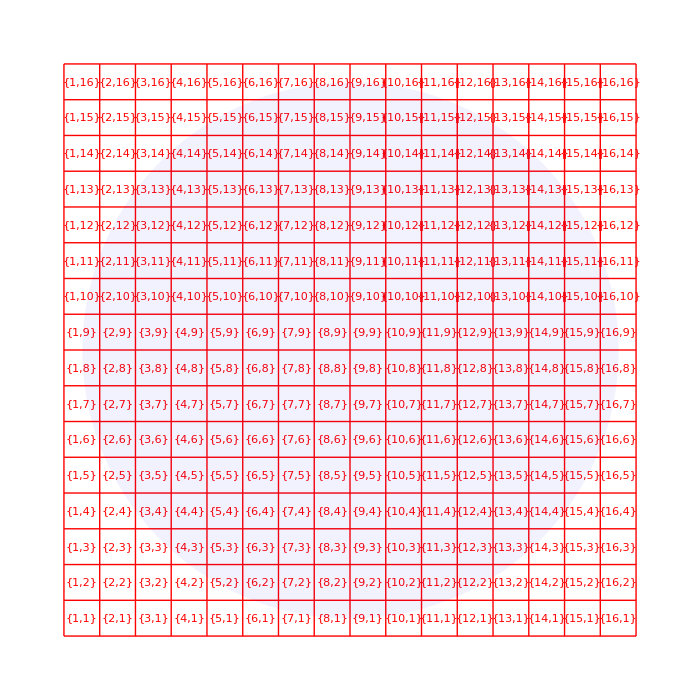

```mathematica
Graphics[{Red,camPixels2D,Blue,Opacity[0.05],Disk[µLensCtr,rNA]},ImageSize->700]
```

#### Ray positions in entrance face of object space for a single, centrally located microlens

The light blue disk indicates the range of possible positions of rays that pass through the center of object space and through the aperture of the microscope objective lens.

voxPitchGraphics = 25

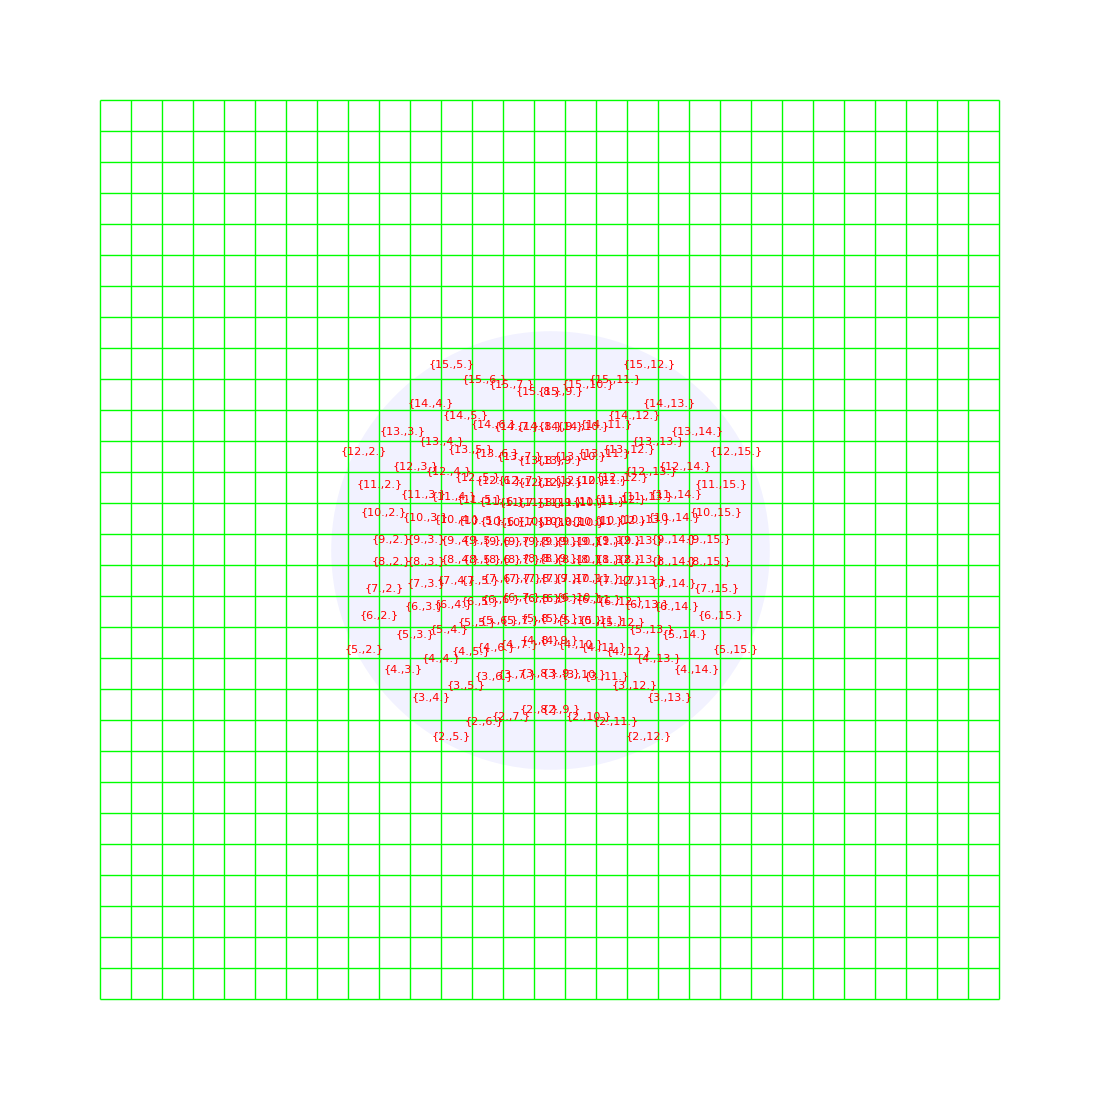

```mathematica
(*Ray positions in Entrance Face, Text shows the indices in camera pixel array*)
Print["voxPitchGraphics = ",voxPitchGraphics];
Graphics[{Blue,Opacity[0.05],Disk[Drop[volCtrGraphics,1],volCtrGraphics[[1]]Tan[ArcSin[naObj/nMedium]]],
			Green,Opacity[1],entranceFace2DGraphics,
			Red,Table[Text[camRayEntranceGraphics[[i,1]],Drop[camRayEntranceGraphics[[i,2]],1]],{i,Length[camRayEntranceGraphics]}]},
	PlotRange->All,ImageSize->1100]
```

The rays are selected to arrive at the square grid of the sensor array, 16 x 16 pixels behind a single microlens, one ray per pixel. The square geometry at the sensor plane turns into a pincushion distortion at the entrance plane to object space, due to the Abbe sine condition that is followed in the design of the microscope objective lens.

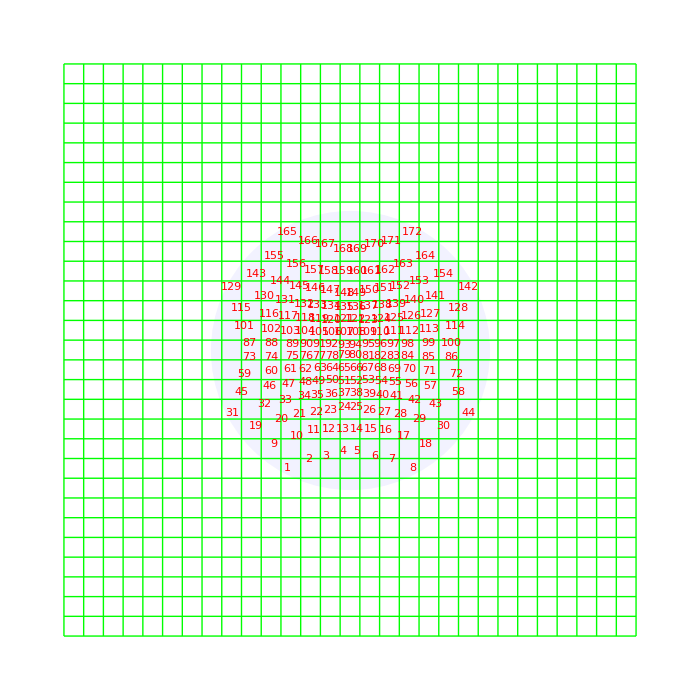

```mathematica
(*Ray positions in Entrance Face, Text shows the ray number*)
Graphics[{Blue,Opacity[0.05],Disk[Drop[volCtrGraphics,1],volCtrGraphics[[1]]Tan[ArcSin[naObj/nMedium]]],
			Green,Opacity[1],entranceFace2DGraphics,
			Red,Table[Text[i,Drop[camRayEntranceGraphics[[i,2]],1]],{i,Length[camRayEntranceGraphics]}]},
	PlotRange->All,ImageSize->700]
```

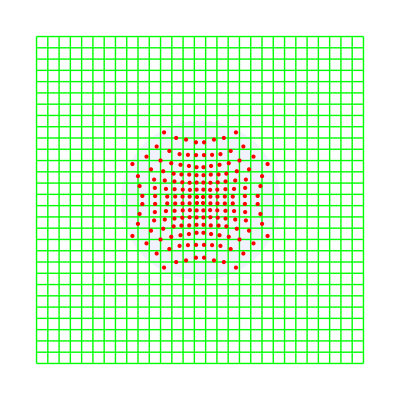

```mathematica
(*Ray positions in Entrance Face*)
Graphics[{Blue,Opacity[0.05],Disk[Drop[volCtrGraphics,1],volCtrGraphics[[1]]Tan[ArcSin[naObj/nMedium]]],
			Green,Opacity[1],entranceFace2DGraphics,
			PointSize[Large],Red,Table[Point[Drop[camRayEntranceGraphics[[i,2]],1]],{i,Length[camRayEntranceGraphics]}]},
	PlotRange->All]
```

The radius of the blue disk and range of ray positions in the entrance face scales with the refractive index (nMedium) of the object space medium and the numerical aperture (naObj) of the microscope objective. For a given naObj = 1.2 and oil (nMedium = 1.52) as the object space medium, the range is much smaller than for water (nMedium 1.33).

Radius of blue disk and range of ray positions for nMedium=1.33 and naObj=1.2

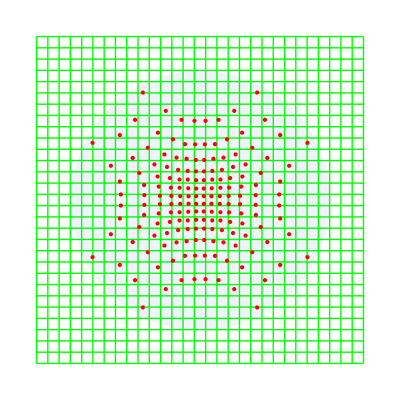

```mathematica
(*Temporarily change nMedium=1.33 and naObj=1.2 and note the difference to nMedium of oil*)
Print["Radius of blue disk and range of ray positions for nMedium=1.33 and naObj=1.2"];
tmp1=nMedium;tmp2=naObj;
nMedium=1.33;naObj=1.2;
camPixRays=Table[If[(tmp=Sqrt[(i-0.5-µLensCtr[[1]])^2+(j-0.5-µLensCtr[[2]])^2])>rNA,{Null},
	{ArcTan[i-0.5-µLensCtr[[1]],j-0.5-µLensCtr[[2]]]/Degree,ArcSin[tmp/rNA*naObj/nMedium]/Degree}//Round],{i,nrCamPix},{j,nrCamPix}];
camRayEntranceGraphics:=Flatten[Table[If[camPixRays[[i,j]]=={Null},,{{i,j},
		{0,volCtrGraphics[[1]]*Tan[camPixRays[[i,j,2]]Degree]Sin[camPixRays[[i,j,1]]Degree]+volCtrGraphics[[2]],
		volCtrGraphics[[1]]*Tan[camPixRays[[i,j,2]]Degree]Cos[camPixRays[[i,j,1]]Degree]+volCtrGraphics[[3]]}}],{i,nrCamPix},{j,nrCamPix}]//N,1]//DeleteCases[Null]
Graphics[{Blue,Opacity[0.05],Disk[Drop[volCtrGraphics,1],volCtrGraphics[[1]]Tan[ArcSin[naObj/nMedium]]],
			Green,Opacity[1],entranceFace2DGraphics,
			PointSize[Large],Red,Table[Point[Drop[camRayEntranceGraphics[[i,2]],1]],{i,Length[camRayEntranceGraphics]}]},
	PlotRange->All]
nMedium=tmp1;naObj=tmp2;
camPixRays=Table[If[(tmp=Sqrt[(i-0.5-µLensCtr[[1]])^2+(j-0.5-µLensCtr[[2]])^2])>rNA,{Null},
	{ArcTan[i-0.5-µLensCtr[[1]],j-0.5-µLensCtr[[2]]]/Degree,ArcSin[tmp/rNA*naObj/nMedium]/Degree}//Round],{i,nrCamPix},{j,nrCamPix}];
camRayEntranceGraphics:=Flatten[Table[If[camPixRays[[i,j]]=={Null},,{{i,j},
		{0,volCtrGraphics[[1]]*Tan[camPixRays[[i,j,2]]Degree]Sin[camPixRays[[i,j,1]]Degree]+volCtrGraphics[[2]],
		volCtrGraphics[[1]]*Tan[camPixRays[[i,j,2]]Degree]Cos[camPixRays[[i,j,1]]Degree]+volCtrGraphics[[3]]}}],{i,nrCamPix},{j,nrCamPix}]//N,1]//DeleteCases[Null]
```

#### Rays in object space

The graphics below shows the complete object volume, roughly 250µm x 700µm x 700µm with a blue ray and its two polarization components in red that will be turned parallel to the Y- and Z-axis after the ray is redirected by the objective lens to run parallel to the X-axis of the laboratory frame of reference.

```mathematica
rayNr=1;(*rayNr=17 is camPixRays[[4,3]], rayNr=75 extends nearly parallel to x-axis*)
Print["voxPitchGraphics = ",voxPitchGraphics];
Graphics3D[{
	Magenta,Opacity[0.2],
	objectCubeGraphics,
	Blue,Opacity[0.02],
	EdgeForm[],Cylinder[{{0,volCtr[[2]],volCtr[[3]]},{0.1,volCtr[[2]],volCtr[[3]]}},volCtr[[1]]Tan[ArcSin[naObj/nMedium]]],
	Opacity[1],Green,
	entranceFaceGraphics,
	exitFaceGraphics,
	Opacity[1],Blue,Thick,
	Arrow[{rayEnter[[rayNr]],rayExit[[rayNr]]}] ,
	Arrowheads[Medium],Red,
	tmpRotMInv=Inverse[RotationMatrix[{rayExit[[rayNr]]-rayEnter[[rayNr]],{1,0,0}}]];
	tmp1=tmpRotMInv.{0,1,0};tmp1=50tmp1/Norm[tmp1]+volCtr;
	Arrow[{volCtr,tmp1}] ,
	tmp2=tmpRotMInv.{0,0,1};tmp2=50tmp2/Norm[tmp2]+volCtr;
	Arrow[{volCtr,tmp2}] 
},Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->400]
```

voxPitchGraphics = 25

-Graphics3D-

The Y-Z object planes thisEntranceFaceGraphics and thisExitFaceGraphics illustrate the Y-Z object planes for which the ray coordinates thisRayEnter and this RayExit are calculated in the Generator routine. The two Y-Z planes  delimit the sample volume in the x-direction and the ray tracing routine is only done through voxels between these two planes.

```mathematica
(*Graphics of voxels touched by a ray, uses voxPitch for simulation*)
rayNr=1; 
smpBoxNrGraphics={5,5,5};  (*extend of sample box along X, Y, Z direction in units of voxPitchGraphics*)
smpBoxVolNrGraphics=Transpose[{voxNrCtrGraphics-smpBoxNrGraphics/2,voxNrCtrGraphics+smpBoxNrGraphics/2}]//Round;  (*sample box in object space voxel numbers*)
thisEntranceFaceGraphics={Green,Thick, (*thisEntranceFaceGraphics illustrates the Y-Z object plane for which the ray coordinates thisRayEnter are calculated in the Generator routine*)
	Line[{{smpBoxVolNrGraphics[[1,1]],0,0},{smpBoxVolNrGraphics[[1,1]],voxNrYZGraphics,0},{smpBoxVolNrGraphics[[1,1]],voxNrYZGraphics,voxNrYZGraphics},{smpBoxVolNrGraphics[[1,1]],0,voxNrYZGraphics},{smpBoxVolNrGraphics[[1,1]],0,0}}],
	Thin,Table[Line[{{0,1,0}*i+{smpBoxVolNrGraphics[[1,1]],0,0},{0,1,0}*i+{0,0,voxNrYZGraphics}+{smpBoxVolNrGraphics[[1,1]],0,0}}],{i,0,voxNrYZGraphics}],
	Table[Line[{{0,0,1}*i+{smpBoxVolNrGraphics[[1,1]],0,0},{0,0,1}*i+{0,voxNrYZGraphics,0}+{smpBoxVolNrGraphics[[1,1]],0,0}}],{i,0,voxNrYZGraphics}]};
thisExitFaceGraphics={Green,Thick, (*thisExitFaceGraphics illustrates the Y-Z object plane for which the ray coordinates thisRayExit are calculated in the Generator routine*)
	Line[{{smpBoxVolNrGraphics[[1,2]],0,0},{smpBoxVolNrGraphics[[1,2]],voxNrYZGraphics,0},{smpBoxVolNrGraphics[[1,2]],voxNrYZGraphics,voxNrYZGraphics},{smpBoxVolNrGraphics[[1,2]],0,voxNrYZGraphics},{smpBoxVolNrGraphics[[1,2]],0,0}}],
	Thin,Table[Line[{{0,1,0}*i+{smpBoxVolNrGraphics[[1,2]],0,0},{0,1,0}*i+{0,0,voxNrYZGraphics}+{smpBoxVolNrGraphics[[1,2]],0,0}}],{i,0,voxNrYZGraphics}],
	Table[Line[{{0,0,1}*i+{smpBoxVolNrGraphics[[1,2]],0,0},{0,0,1}*i+{0,voxNrYZGraphics,0}+{smpBoxVolNrGraphics[[1,2]],0,0}}],{i,0,voxNrYZGraphics}]};
Print["voxPitchGraphics = ",voxPitchGraphics,"\n","sample box = ",smpBoxVolNrGraphics, " [numbers]"];
mP0=Ceiling[midPoints[rayEnter[[rayNr]]/voxPitchGraphics,rayExit[[rayNr]]/voxPitchGraphics,{1.,1.,1.},smpBoxVolNrGraphics]];(*list of midPoint lists for every ray within naObj centered on volCtrGraphics*)
Graphics3D[{Opacity[0.25],Cuboid[Transpose[smpBoxVolNrGraphics][[1]],Transpose[smpBoxVolNrGraphics][[2]]],
		Opacity[0.5],Table[Translate[Cube[],mP0[[i]]-{0.5,0.5,0.5}],{i,Length[mP0]}],
		Opacity[1],Blue,Thick,Line[{rayEnter[[rayNr]],rayExit[[rayNr]]}/voxPitchGraphics],
		thisEntranceFaceGraphics,
		thisExitFaceGraphics},
		PlotRange->{{0,voxNrXGraphics},{0,voxNrYZGraphics},{0,voxNrYZGraphics}},ImageSize->400]
```

voxPitchGraphics = 25
sample box = {{3,8},{12,17},{12,17}} [numbers]

-Graphics3D-

#### Light Field LC-PolScope

```mathematica
fontSizeParameter=32;spread=1;
optics=Show[{
	lfSensor[34spread,0.5,"Light Field Sensor"],
	tubeLens[20spread,0.5,"Tube Lens"],
	leftCircPolar[13spread,Gray,0.5,"Left Circ. Analyzer"],
	objectiveLens[3spread,0.5],
	slideCoverslipSample[-0.5,0.5],
	condenserLens[-3spread,0.5],
	lcCompensatorBonded[-14spread,Gray,0.5,"LC-Polarizer"],
	ifFilter[-24spread,Green,0.5,"Interference Filter"],
	collectorLens[-32spread,0.5],
	bulb2[-40spread,0.5]},
PlotRange->{{-60,15},{-10,10},{-45spread,40spread}},Boxed->False,ViewPoint->{0,-Infinity,0},ImageSize->600]
```

-Graphics3D-

```mathematica
Show[optics,ViewPoint->{1.3,-2.4,2}]
```

-Graphics3D-

```mathematica
(*When calculating optics, make spread=1*)
Show[{optics,Graphics3D[{Thick,Green,Cylinder[{{0,1,-40},{0,-1,-40}},0.5],
	Line[{{-0.5,0,-40},{-4.8,0,-33},{-5.2,0,-31},{-4.8,0,-6},{-4,0,-3},{0,0,0}}],
	Line[{{0.5,0,-40},{4.8,0,-33},{5.2,0,-31},{4.8,0,-6},{4,0,-3},{0,0,0}}],
	Line[{{0,0,0},{-4,0,3},{-5.2,0,6},{-5,0,19.3},{-4.8,0,20.8},{1.1,0,35.5}}],
	Line[{{0,0,0},{4,0,3},{5.2,0,6},{5,0,19.3},{4.8,0,20.8},{-1.1,0,35.5}}],
		EdgeForm[{Thick,Opacity[1],Red}],FaceForm[Opacity[0]],Cylinder[{{0,-0.1,33.5},{0,-0.15,33.5}},7.5]}]},
	PlotRange->{{-46,15},{-10,10},{-45,42}},ImageSize->800]
```

-Graphics3D-

```mathematica
tmp=Show[{lfSensor[1.5,0.5,"NoName"],
		Graphics3D[{Green,Opacity[1],
			Thick,Line[{2.4{0.91,0,-3},{-0.91,0,3}}],
			Line[{{0.5,0,0}+2.4{0.91,0,-3},{0.5,0,0},{-0.91,0,3}}],Line[{{-0.5,0,0}+2.4{0.91,0,-3},{-0.5,0,0},{-0.91,0,3}}],
			Thick,Line[{2.4{-0.91,0,-3},{0.91,0,3}}],
			Line[{{0.5,0,0}+2.4{-0.91,0,-3},{0.5,0,0},{0.91,0,3}}],Line[{{-0.5,0,0}+2.4{-0.91,0,-3},{-0.5,0,0},{0.91,0,3}}],
			EdgeForm[{Thick,Opacity[1],Red}],FaceForm[Opacity[0]],Cylinder[{{0,-0.1,0},{0,-0.15,0}},7.5]}]},
	PlotRange->{{-7.6,7.6},{-7.6,7.6},{-7.6,7.6}},Boxed->False,ViewPoint->{0,-Infinity,0}]
```

-Graphics3D-

```mathematica
anotThick=0.002;
Show[{tmp,
	Graphics3D[{Black,Thickness[anotThick],Arrowheads[{-10anotThick,10anotThick}],
	Line[{{-1,0,3.5},{-1,0,4.5}}],Line[{{1,0,3.5},{1,0,4.5}}],Arrow[{{-1,0,4},{1,0,4}}],
	Text[Style["100µm",18,Background->White],{0,0,5}],Text[Style["16 by 16 pixels",18,Background->White],{0,0,6.2}],
	Line[{{-8,0,0},{-10,0,0}}],Line[{{-8,0,3.0},{-10,0,3.0}}],Arrow[{{-9,0,0},{-9,0,3.0}}],Text[Style["2.5mm",18,Background->White],{-9,0,1.5}]}]},
PlotRange->All]
```

-Graphics3D-